```mathematica
Quit[]
```

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
(* trigger autoload Failure formatting *)
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

## update

```mathematica
PacletUninstall["CodeInspector"]
```

PacletUninstall::notfound: Paclet CodeInspector not found.

$Failed

```mathematica
PacletInstall["/Users/brenton/development/stash/COD/codeinspector/build/paclet/CodeInspector-999.paclet"]
```

PacletObject[CodeInspector,999,<>]

```mathematica
PacletDirectoryAdd["/Users/brenton/development/stash/COD/codeinspector/CodeInspector"];
```

```mathematica
FindFile["CodeInspector`"]
```

/Users/brenton/development/stash/COD/lint/Lint/Kernel/Lint.wl

```mathematica
PacletUpdate["CodeInspector","UpdateSites"->True]
```

PacletObject[Lint,0.15,<>]

## Init

```mathematica
$MessagePrePrint=.
```

```mathematica
Off[General::stop]
```

The AST package must be built first. Change these paths to point to your location of ASTTools.

```mathematica
Needs["CodeInspector`"]
Needs["CodeInspector`ImplicitTimes`"]
```

```mathematica
installation=$InstallationDirectory<>"/";
```

```mathematica
protos="/Users/brenton/Library/Mathematica/ApplicationData/StashLink/Prototypes/";
```

```mathematica
stash="/Users/brenton/development/stash/";
```

```mathematica
cvs="/Users/brenton/development/cvs-development/";
```

```mathematica
github="/Users/brenton/development/github-development/";
```

```mathematica
other="/Users/brenton/development/other-development/";
```

```mathematica
examples="/Users/brenton/Downloads/WLCodeExamples/";
```

```mathematica
(*lineHashExclusions=<|
(*kernelMain / protos*)
"Kernel/StartUp/Algebra/NumberField.m"->{"03d1240b54171896"},
"Kernel/StartUp/Control/CodeGeneration.m"->{"19412d627d6b7e46","694323f420e68a25"},
"Kernel/StartUp/Convert/NBMLConvert.m"->{"31f2e8ea294f80bd"},
"Kernel/StartUp/DataPaclets/PsychrometricPropertyData.m"->{"6999fce83dac548b","62238af94392477c","5f23d2758de3a21f",
"40f8d6c9b6d4b08a"},
"Kernel/StartUp/DateTime/CalendarAstronomy.m"->{"31a45a1c1b35fda4","173ed72efc7557a7"},
"Kernel/StartUp/DSolve/DSolveIntegroDifferentialEquation.m"->{"70806c5ac6cccbc6"},
"Kernel/StartUp/Explore/Explore.m"->{"204f684487679053"},
"Kernel/StartUp/Explore/PlotExplorer.m"->{"04983530c6c11391"},
"Kernel/StartUp/FunctionInterpolation.m"->{"4599dd69670d0292"},
"Kernel/StartUp/GIS/GeoModel.m"->{"1c27000519cde9ed","10c8a44b236ba029","62d9fd8900ee8261"},
"Kernel/StartUp/GIS/GeoProjections.m"->{"7a14bc508f22709f","16911bb751b91ee7","4ab33b1dd799a83b","0637c66fd64e707e","4ab33b1dd799a83b",
"7b1ba946278cbf17","069bf6e928e916b2","3ad653f01f4d5f33","27b3a9c0108ed1d9","466dc1ee9093b6db","6635fbe2602a13ba"},
"Kernel/StartUp/Graphics/GraphicsFormat.m"->{"3f105940ae99f908","5024bd6c9eeaa56a","073b391afdc9e837","6440cadea419ea41","2c1db2175672be73"},
"Kernel/StartUp/ImageProcessing/CompositionOps/Compose.m"->{"3fb6e2e0b3ea6a14"},
"Kernel/StartUp/ImageProcessing/Matrices/Common.m"->{"76146a30598981ea","7b13c36587c903e0","6efd63b1fabadf50","78abe098d3fa2871"},
"Kernel/StartUp/Integrate/trig.m"->{"312f6a2a05f7a632"},
"Kernel/StartUp/LinearAlgebra/TransformConstructors.m"->{"014b2c47dae470d2","014b2c47dae470d2","72725bb3496e1116"},
"Kernel/StartUp/Manipulate.m"->{"63c6508d29a231dc","63c6508d29a231dc","21ebb11eb5eb8ff3","3b6779e059e8cafc",
"0c7d9bf871d837b7","50f1486f6187d938","2e8fd78da03300b3","3f745ba41220d3a6","7f9855eae09a71b5","7bd2fd3eff54b2d4","7ffa231626579ddd"},
"Kernel/StartUp/NDSolve/EquationProcessing/DiscontinuityValues.m"->{"5fb198b362503f4b","26468f9b95a56282"},
"Kernel/StartUp/NDSolve/FEM/FEMBoundaryConditions.m"->{"6708e1f79d36c5d2"},
"Kernel/StartUp/NDSolve/FEM/FEMDiscretization.m"->{"63df233ff906cdba","2de223d7462bc969","5377d7bb94813731","31d1946443afe858","39bbde8a59d1cfa1"},
"Kernel/StartUp/NDSolve/FEM/FEMMesh.m"->{"77b81b15ce83c44f","0f0a5515359f1ba1","01d8b85bc47897c6","4ae6660d412a6cf4","7ca7dbcc62b27784"},
"Kernel/StartUp/NDSolve/FEM/PDEParser.m"->{"61d265e8b87ca6f4","6928ae8049c0eb94"},
"Kernel/StartUp/Network/GraphBoxes.m"->{"44471c9adf36998f","41d6756484bc28c1","41d6756484bc28c1"},
"Kernel/StartUp/Network/GraphChart.m"->{"52ad6f2cf8fc9508"},
"Kernel/StartUp/NIntegrate/SimplexQuadrature.m"->{"2a1e92e5bdb9b59f"},
"Kernel/StartUp/Optimization/NMinimize.m"->{"31f2e8ea294f80bd","33c0e18754f1ca87","05fbc58560d62489"},
"Kernel/StartUp/Reduce/Optimization.m"->{"7354fe94335abd0e"},
"Kernel/StartUp/Reduce/Thue.m"->{"273f4daef0b9ac4e"},
"Kernel/StartUp/Reduce/TRoots.m"->{"6bf17ab528ab3634","0ae2ab78930a6b4b"},
"Kernel/StartUp/Regions/Meshes/MeshGraphicsBox.m"->{"15012f9b6e615e3a","4b582a793c7c4e50"},
"Kernel/StartUp/Regions/Meshes/MeshUtilities.m"->{"7f306bf072dd37b5"},
"Kernel/StartUp/Regions/RegionFunctions/RandomPoint.m"->{"4616b599f2fa37d6"},
"Kernel/StartUp/Regions/RegionGraphics/RegionGraphicsBox.m"->{"338667ce2d251209"},
"Kernel/StartUp/Regions/RegionOperations/SRRelations.m"->{"1c8c83222f5d0c82"},
"Kernel/StartUp/Regions/RegionTransforms/AffineTransforms.m"->{"2fc60f01bef7a902","4222fdf69a8baeb0","6d2e16e85a7da416",
"2ea17edaba8aba31"},
"Kernel/StartUp/Regions/RegionUtilities/SpecialRegions.m"->{"33c67ab17bccac81","6f7b9138db2656ae"},
"Kernel/StartUp/RSolve/RecurrenceTable.m"->{"014747e395d6518b"},
"Kernel/StartUp/Sound/AudioCapture.m"->{"70b00628974564e6"},
"Kernel/StartUp/Sound/AudioUtilities.m"->{"0c6bdb7c4ab10f36"},
"Kernel/StartUp/SpatialAnalysis/PointProcesses/PointProcesses.m"->{"40c32a0afe9384af","550af0dedee0afb9","22e6927b43e01027",
"284d0d33f595fcdb","6bd16240c77f9482","03c86d49bde23991","7ca7fd92e93d67f5"},
"Kernel/StartUp/SpecialFunctions/Spheroidal.m"->{"6e16f82800922386","7906253e39b74fd7","08b3b641ba36d555","03167346aea55881",
"76bc31f32ce72935","185c0324aee7fad0","2985a2a42076c0d3","17f8da2ff386525e","7a2d0f7e605f7eef","7497735755f9e9cf","2e3ff306dc7be3cd",
"0bad421509a91f64","2e3ff306dc7be3cd","0bad421509a91f64","78a49a1be39f66ac","2b53ad8ed694d4af","78a49a1be39f66ac","02fde28cdc8f8515",
"02fde28cdc8f8515"},
"Kernel/StartUp/Statistics/ContinuousDistributions/MultinormalDistributions.m"->{"18b70af3b9aa0f27","1023469f6ea06c4a"},
"Kernel/StartUp/Statistics/NonparametricDistributions/HistogramDistribution.m"->{"0fe8fdcd7760d2cb"},
"Kernel/StartUp/Statistics/Solvers/RandomVariate.m"->{"49ab5df2e8ce36ff"},
"Kernel/StartUp/Sum/SumFiniteSpecialRules.m"->{"08dc11ca3cd2fc44","4109b1ef6072f1b5","16132a05552dd3b0","0e1b0aefcfe083c9",
"4d1cc96fc29f93ef","120217d1ac98d252","51c61a396b951c18","050c056a38b6efa2","77da786bdf4b07e7","2388c63276ff1ed8","480b9699e7ec777d",
"0c74efa034f34341","469e6b373339a737","3c9814cf6756ca4a","30db291a9cf2752e"},
"Kernel/StartUp/Sum/SumInfiniteSpecialRules.m"->{"009b8100f4b38d4e","33eec2bfb4fb29be","1c66ca31096b4421","340a70642d837be3",
"1cd1f097208aa8be","1d30b8df4ebb5fc5","3261b5e0bf425424","1668474f3ea06acf","18c21cb746c4956d","01672fe76d75bb57","55e55046d08fb2d9",
"463ff09673a32ef5","5384051f170c90d3","65927912de0c6a4b","1ebf64bb9169f0bf","5b475f05ba1dceb3","3f5cfe0face42598","0dc05741a3d477b5",
"720a18b2fcabb4d3","1e79bc820b2afb07","64bd987050fc090d","5f9b01f249e3fec3","01e966b9ca6dbeca","5bbd805809ab8919","55fa242385113005",
"112c28588b8ebbd5","14b570c669f658c2","7720cbbc036ce346","35e674e891a87962","7e4130936ee98e84","37b3067ce5d305f6","5e74cc8f396822d0",
"309087f00a929548","0f5235e753aa120f","379f64387817033d","36f8a1a0bad13b2f","18884cbd72648cbb","6518ec105bcd8293","73b8a2d10a0b779a",
"393c0afbfddd8109","5bec2a3708ed6cf8","544eca99045d98c0","35d50fa3cc60d710","0af15edc3a2ea149","2a2c4348641806bc","6d1f39199d250a45",
"29c090d03c69b7d8","0430419de17637a3","1f78eca9ca7a4729","2e552ed214f34275","5d882a9a6b0ac211","3419bf4dc8f7dfec","6b0844d984ad016a",
"0921cd365e323fde"},
"Kernel/StartUp/SymbolicTensors/SymbolicTensors.m"->{"05fec030e95e6476","3eb8e9739ab3e438"},
"Kernel/StartUp/Typeset/Dynamic.m"->{"57f673e76ea2cc7c","72b37c39f1696743","289982d63417f317"},
"Kernel/StartUp/Typeset/TypesetInit.m"->{"11e7d903a5843287","7373773d50cfdf2a"},
"Kernel/StartUp/Typeset/SpokenString.m"->{"33a602646fbb3c07"},
"Kernel/StartUp/Visualization/BarChart3D.m"->{"3203e7bd35a5e4f0","3203e7bd35a5e4f0","7dcd17b4dc392932"},
"Kernel/StartUp/Visualization/Gauges.m"->{"39f354a522826d6a","30fbab6141beb9a6","4482be4096d686e0","72fcd59133313277",
"59ac5f4b7d8f64c8","324903fb58803084","500eed1e82e8688b","02031082ce4514d7"},
"Kernel/StartUp/Wavelets/BattleLemarieWavelet.m"->{"49037cf904a93e45","3b8fe5be4be833ef"},
"Kernel/StartUp/Wavelets/LiftingFilter.m"->{"38731099c22fe90d"},
"Messages/errmsg.m"->{"70e96836925e4183","68022076f22e34f1","0ca5c2437e5f1330","1ed9c6e1816179a3","414b1647a49bb7fd","026120075106fd13",
"0b886d39b01873a7"},

(* installation *)
"AddOns/Applications/CompiledFunctionTools/CompiledFunctionTools.m"->{"0da7a7d28cfca989"},
"AddOns/Applications/CompiledFunctionTools/PrintCode.m"->{"2ee70999758761e4"},
"AddOns/ExtraPackages/DifferentialEquations/NDSolveProblems.m"->{},
"AddOns/Packages/Combinatorica/Combinatorica.m"->{"4c77ed39f6de1bbf"},
"AddOns/Packages/FiniteFields/FiniteFields.m"->{"2b861e17c93dc12a","017a494002e954e2"},
"AddOns/Packages/FourierSeries/FourierSeries.m"->{},
"AddOns/Packages/LinearRegression/LinearRegression.m"->{"2a72cde271a6182f"},
"AddOns/Packages/MultivariateStatistics/MultiDescriptiveStatistics.m"->{"18fdc749f03c0145"},
"AddOns/Packages/NonlinearRegression/NonlinearRegression.m"->{"781b523611463a94"},
"AddOns/Packages/Splines/Splines.m"->{"3bbaf0e5bd799e3c"},
"AddOns/Packages/VariationalMethods/VariationalMethods.m"->{"639685c94ca4306e"},
"SystemFiles/Components/CCodeGenerator/CCodeGenerator.m"->{"78497442d3f98d1b"},
"SystemFiles/Components/Compile/AST/Macro/Builtin/Conditional.m"->{"1d73c3819ade1768","1e0ad42179349164","0db845947764e204",
"0bf9ba4da619f4a3"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Break.m"->{"64499f2d5c2d329e"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Continue.m"->{"335607c5839b8cbf"},
"SystemFiles/Components/Compile/Core/IR/Lower/Primitives/Return.m"->{"3b9c3fb7da3d5426"},
"SystemFiles/Components/Compile/Utilities/Language/SymbolAreasTable.m"->{"55eac21c2ba1bb7f","2d3d344d0445c106",
"42f97ad40a0821d4"},
"SystemFiles/Components/CompileUtilities/RuntimeChecks/RuntimeChecks.m"->{"0f40561fc4b61bbe","2dfea9ca8b7e9ec2",
"54d7b7b60d50741a","10c16e404e4c7412","165bc22739e6fa11","0f831b782569644e"},
"SystemFiles/Components/FunctionResource/Kernel/Utilities.m"->{"2cc0df58b7106f2e"},
"SystemFiles/Components/NeuralNetworks/MXNet/ToPlan.m"->{"225c6ca998056014","13c44f36e1a68511"},
"SystemFiles/Components/NeuralNetworks/NetTrain.m/JIT.m"->{"5087244a89f175d7","72558357da1e3c14","2528f9b225dac1f6",
"409452941c481b4b"},
"SystemFiles/Components/NeuralNetworks/Types/Coerce.m"->{"6cbcc1bacc9abad0","5da750900e4b0c93","3444c9323cc3f1a9",
"0271ba3207bba61f","0922816608f8da27"},
"SystemFiles/Components/NeuralNetworks/Types/Predicates.m"->{"5f3ef3955f71dcbe","369d54e3e40141b4","28e9cba7b120d9ae",
"734829e822cd569a","365bcb383e4d8bdb","54f3578146c96f37","528b2f425df6d9cd","557d176b6b2360b8","6c11c4c9de755117",
"3ed9c254b70e14b3","05fca00977088c72","24424346dc2c3c83","457dead36e959162","1d60aacf12acbdd4","7c63017a335427ca",
"75fd81bd944a22f4","09987fecf69372cc","09b638849bfd73e4","1f3386e1cb7ea1c6","284459d5c9d47a80",
"375689a102c07934","457ef592ca9338cd","177a4e532d1ecee9","071f231c47fd18be","2e2a03e35a605425","2f67aa096ed90221"},
"SystemFiles/Components/NeuralNetworks/Types/Properties.m"->{"28587a95a919c11c","4675793b836de53e","734829e822cd569a",
"31dc3cb00a1358ac","40275c504d7191c5","5087244a89f175d7","4c8634f4d0b61ad8","10f37f55b34429ba","54bdcb4da83c16dd",
"549d1d5e6fbffbca"},
"SystemFiles/Components/NeuralNetworks/Types/Random.m"->{"3f0b54e666328d26","0bc6b7514e62c98c","2373704cfd1fd33a",
"75a1121337c1ad03","0669da00893fbb21","492dfb7c60ce1f5c","3afa900664d8a6f3","4fb38cbd35da0cdf","53b84e89c22b77a7",
"6e882b56777d5e5b","063b8c620220f928","6d3174c97f5c9ee6","74cd0f4217fd7b71","4ed3a9d412f4ec6f","1a6c7be4442d85ff"},
"SystemFiles/Components/NeuralNetworks/Types/TypeForm.m"->{"63ba7b4cb5c1faf8","5af263d8a51abaa9","2a6a2b31c958546b",
"7f60794836b6c443","29feed4f7a833f29","59409e0c21b05eb6","393100f1101d9ffb","7e98869700297526","74cd0f4217fd7b71",
"4190e3d36d0835f3","6ff610a5ba1a66da","0641cbba44f4ca04","3a17989bc0e27dd6"},
"SystemFiles/Components/NeuralNetworks/Types/Types.m"->{"75d05b7eafb55daa","55ff8aa2423d5468","5d4fd4861152a641",
"17448ddada285ac6","343c0b3929312df2"},
"SystemFiles/Components/WebAudioSearch/Kernel/WebAudioSearch.m"->{"5dc72403f4780fa1","085f5cdd394e3d7c","2ad8f93badfad71a"},
"SystemFiles/Devices/DeviceDrivers/Serial.m"->{"57ff70ba95d4c2ec"},
"SystemFiles/Kernel/TextResources/English/Messages.m"->{"70e96836925e4183","68022076f22e34f1","1ed9c6e1816179a3",
"0b886d39b01873a7","0ca5c2437e5f1330","414b1647a49bb7fd","026120075106fd13"},
"SystemFiles/Links/Databases/Databases/Common/Common.m"->{"0399a740b3cde7f1","7e16465b0f01aedf"},
"SystemFiles/Links/Databases/Databases/Database/Compiler/ExpressionCompiler.m"->{"73e4b3175535ddf4"},
"SystemFiles/Links/GPUTools/CompileCodeGenerator.m"->{"78497442d3f98d1b"},
"SystemFiles/Links/GPUTools/SymbolicGPU.m"->{"5bc5be7e7db96d42","79ae15d998ad6b9e","6e28d7b590e2b94a","42cba421cd99c297","569eb9731485259d"},
"SystemFiles/Links/GPUTools/WGLPrivate.m"->{"1b3e9c9e332d4f98","0f2dbae3e06207b8","177367bae68f5d49","79581a5b6f95c7da","497e31b051e5e3dd",
"50a5caab2dcab938","2c35e17facaa7fa3","255873cd4cd2cfaa","47fb215e76336e6e","47fb215e76336e6e","114fa7b54fce134f","5081c6edc7560ead",
"03926f8b9ed14b88","104e7ab00261eb67"},
"SystemFiles/Links/IPOPTLink/IPOPTLink.m"->{"37614a48c96c3933","36c30c2a6a2818d6","36c30c2a6a2818d6","36c30c2a6a2818d6","4eadd2d17535cb38"},
"SystemFiles/Links/SecureShellLink/Kernel/Remote.wl"->{"326714fee09a9ac7","326714fee09a9ac7"},
"SystemFiles/Links/SerialLink/SerialLink.m"->{"6fce25b343c1b272","240e812787f09206"},
"SystemFiles/Links/WebServices/Kernel/Implementation.m"->{"3559460bc280923e"},

(*repos*)
"Compile/Compile/AST/Macro/Builtin/Conditional.m"->{"1d73c3819ade1768","1e0ad42179349164","0db845947764e204",
"0bf9ba4da619f4a3"},
"Compile/Compile/Core/CodeGeneration/Backend/CXX/CXX.m"->{"66b82c229e584d85","58744f56b79779e9"},
"Compile/Compile/Core/IR/Lower/Primitives/Break.m"->{"64499f2d5c2d329e"},
"Compile/Compile/Core/IR/Lower/Primitives/Continue.m"->{"335607c5839b8cbf"},
"Compile/Compile/Core/IR/Lower/Primitives/Return.m"->{"3b9c3fb7da3d5426"},
"Compile/Compile/Utilities/Language/SymbolAreasTable.m"->{"55eac21c2ba1bb7f","2d3d344d0445c106",
"42f97ad40a0821d4"},
"CompileUtilities/CompileUtilities/RuntimeChecks/RuntimeChecks.m"->{"0f40561fc4b61bbe","2dfea9ca8b7e9ec2",
"54d7b7b60d50741a","10c16e404e4c7412","165bc22739e6fa11","0f831b782569644e"},
"CUDACompileTools/CUDACompileTools/Transforms/InstantiateMap.m"->{"30b602d59b8145a6","4ded2efc42f62f63","1b2faae3520c3558"},
"DeviceDrivers/Serial.m"->{"57ff70ba95d4c2ec"},
"GeneralUtilities/GeneralUtilities/Control.m"->{"403ab287349342f8","171897441bde5358","7afc74af8d8d568f"},
"GeneralUtilities/GeneralUtilities/EvaluationInformation.m"->{"0510938e465f7299","3138797ad33251d6"},
"GeneralUtilities/GeneralUtilities/Formatting.m"->{"05ffd75ea43a770c","5a53261bf894faa7"},
"GeneralUtilities/GeneralUtilities/Stack.m"->{"3f57b710dd40818c","75dfa25a918b48ff","14c8217dc87084cb"},
"GeneralUtilities/Tests/TextString.m"->{},
"NeuralNetworks/NeuralNetworks/MXNet/ToPlan.m"->{"225c6ca998056014","13c44f36e1a68511"},
"NeuralNetworks/NeuralNetworks/NetTrain.m/JIT.m"->{"5087244a89f175d7","72558357da1e3c14","2528f9b225dac1f6",
"409452941c481b4b"},
"NeuralNetworks/NeuralNetworks/Types/Coerce.m"->{"6cbcc1bacc9abad0","5da750900e4b0c93","3444c9323cc3f1a9",
"0271ba3207bba61f","0922816608f8da27"},
"NeuralNetworks/NeuralNetworks/Types/Predicates.m"->{"5f3ef3955f71dcbe","369d54e3e40141b4","28e9cba7b120d9ae",
"734829e822cd569a","365bcb383e4d8bdb","54f3578146c96f37","528b2f425df6d9cd","557d176b6b2360b8","6c11c4c9de755117",
"3ed9c254b70e14b3","05fca00977088c72","24424346dc2c3c83","457dead36e959162","1d60aacf12acbdd4","7c63017a335427ca",
"75fd81bd944a22f4","09987fecf69372cc","09b638849bfd73e4","1f3386e1cb7ea1c6","284459d5c9d47a80","375689a102c07934",
"457ef592ca9338cd","177a4e532d1ecee9","071f231c47fd18be","2e2a03e35a605425","2f67aa096ed90221"},
"NeuralNetworks/NeuralNetworks/Types/Properties.m"->{"28587a95a919c11c","4675793b836de53e","734829e822cd569a",
"31dc3cb00a1358ac","40275c504d7191c5","5087244a89f175d7","4c8634f4d0b61ad8","10f37f55b34429ba","54bdcb4da83c16dd",
"549d1d5e6fbffbca"},
"NeuralNetworks/NeuralNetworks/Types/Random.m"->{"3f0b54e666328d26","0bc6b7514e62c98c","2373704cfd1fd33a",
"75a1121337c1ad03","0669da00893fbb21","492dfb7c60ce1f5c","3afa900664d8a6f3","4fb38cbd35da0cdf","53b84e89c22b77a7",
"6e882b56777d5e5b","063b8c620220f928","6d3174c97f5c9ee6","74cd0f4217fd7b71","4ed3a9d412f4ec6f","1a6c7be4442d85ff"},
"NeuralNetworks/NeuralNetworks/Types/TypeForm.m"->{"63ba7b4cb5c1faf8","5af263d8a51abaa9","2a6a2b31c958546b",
"7f60794836b6c443","29feed4f7a833f29","59409e0c21b05eb6","393100f1101d9ffb","74cd0f4217fd7b71",
"4190e3d36d0835f3","6ff610a5ba1a66da","0641cbba44f4ca04","3a17989bc0e27dd6"},
"NeuralNetworks/NeuralNetworks/Types/Types.m"->{"75d05b7eafb55daa","55ff8aa2423d5468","5d4fd4861152a641",
"17448ddada285ac6","343c0b3929312df2"},
"SerialLink/SerialLink/SerialLink.m"->{"6fce25b343c1b272","240e812787f09206"},
"Streaming/Streaming/LazyList/Integration/Packing.m"->{"56cc8189d68e68ce"},
"Streaming/Streaming/Objects/References.m"->{},
"SymbolicMachineLearning/SymbolicMachineLearning/FindFormula/InputArgumentTestFindFormula.m"->{"326714fee09a9ac7",
"31f2e8ea294f80bd","31f2e8ea294f80bd"},
"TypeSystem/TypeSystem/NestedGrid.m"->{"1102829ba555ef0a","337b45658482a540","0126e31743571250","393bc3533d05232d",
"30b52c8e18d84a23","666063adb2147530","5e73236c6f38e2cf","6755030528f12566","73fac8b08b377dfb","0df2019fb2590c36",
"6dd88bf17d80e3ee","276bfb2de7885320","4c57b7c19b76e48f","3a2e18d090a02ff1"},

(*alpha*)
"alphasource/CalculateData/EntityPropertyTable/PhysicalSystemEntity.m"->{"01d6cc28b483714d"},
"alphasource/CalculateIncludes/MathematicalFunctionData/JacobiSymbol.m"->{"260c01c2d6762f58","260c01c2d6762f58","260c01c2d6762f58"},
"alphasource/CalculateParse/GeneralLibrary.m"->{"0d47950b4e1821ab","527d746237686bb9","0b87e244f6360e62","763fd034266517a0"},
"alphasource/CalculateParse/Grammar.m"->{"2b417b85f5b60ab2"},
"alphasource/CalculateParse/TemplateParser4.m"->{"18681de613ddaa16","18681de613ddaa16"},
"alphasource/CalculateScan/ChemicalThermodynamicsScanner.m"->{"2e18556759526e9b"},
"alphasource/CalculateScan/CommonSymbols.m"->{"499ddc8c7d0b96bd","37fb5f08252843d9"},
"alphasource/CalculateScan/Data/GeometryData.m"->{"647513426795059d"},
"alphasource/CalculateScan/FormulaScanner.m"->{"1087fe6f2d24fc16"},
"alphasource/CalculateScan/FunctionalDifferentiationScanner.m"->{"10b697e57d47f040"},
"alphasource/CalculateScan/IteratedObjectsScanner.m"->{"64a1c03013d80191"},
"alphasource/CalculateScan/Packages/Blackbody.m"->{"2e71c84d83bba554"},
"alphasource/CalculateScan/Packages/PlanetaryAstronomy.m"->{},
"alphasource/CalculateScan/ReduceScanner.m"->{"21a376552811e786"},
"alphasource/CalculateScan/StepByStepMath/StepByStepSimplify.m"->{"11a42d4b25a779d2"},
"alphasource/CalculateScan/UnitScannerUnitBases.m"->{"7cdb043b4313f51e"},
"alphasource/CalculateUtilities/DebuggingUtilities.m"->{"53d006cde1d33b88","5913001b08e13dd3"},
"alphasource/CalculateUtilities/DynamicUtilities.m"->{"476898ebd553cc9d"},
"alphasource/CalculateUtilities/FormatUtilities.m"->{"7aca62cf0b05ee19"},
"alphasource/CalculateUtilities/GraphicsUtilities.m"->{"3730df81df2fb4ba","0cb057b476cc324c","038baa7ed2e1895a"},
"alphasource/CalculateUtilities/ImportExport/DataRecognizer.m"->{"666cb9aed60a281a"},
"alphasource/CalculateUtilities/InfrastructureUtilities.m"->{"18b48f4c587e4066","4eb6c88c40274c9c","09720b08c7de115c","2a4aac919205d1d2"},
"alphasource/DataScience/Utils/Language.m"->{"2a8037a4e5b83548","70e3108512e77cd0","13d0c8505832d475","106e59ae5c99765c",
"0d68498b891ea465","626af03fdbf64559"},

(*other*)
"systemmodeler/WL/WSMLink/Diagram/Diagram.m"->{"4a1e9c375885b904"},


Nothing
|>;*)
lineHashExclusions=<||>;
performanceGoal="Quality";
concreteRules=CodeInspector`ConcreteRules`$DefaultConcreteRules;
aggregateRules=CodeInspector`AggregateRules`$DefaultAggregateRules;
abstractRules=CodeInspector`AbstractRules`$DefaultAbstractRules;
```

```mathematica
$AdditionalRules=<||>;
```

```mathematica
Options[lintTest]={"FileNamePrefixPattern"->""};
```

```mathematica
lintTest[fileIn_String,i_Integer,OptionsPattern[]]:=
Catch[
Module[{lints,data,file,prefix,f,byteCount},
file=fileIn;

byteCount=FileByteCount[file];

If[byteCount<CodeInspector`Private`$fileByteCountMinLimit,
Throw[ok]
];
If[CodeInspector`Private`$fileByteCountMaxLimit<byteCount,
Throw[ok]
];

prefix=OptionValue["FileNamePrefixPattern"];

Quiet[
Check[
data=CodeInspectSummarize[File[file],
"LineHashExclusions"->Lookup[lineHashExclusions,StringReplace[file,StartOfString~~prefix->""],{}],
"SeverityExclusions":>severityExclusions,
"TagExclusions":>tagExclusions,
PerformanceGoal:>performanceGoal,
"ConcreteRules":>concreteRules,
"AggregateRules":>aggregateRules,
"AbstractRules":>abstractRules,
Sequence[]];
,
Print[Style[Row[{"index: ",i," ",StringReplace[fileIn,StartOfString~~prefix->""]}],Red]];
Print[Style[Row[{"index: ",i," ",InspectedLineObject::truncation}],Red]];
,
{InspectedLineObject::truncation}
],
{InspectedLineObject::truncation}
];

If[data[[2]]≠{},
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[data]
];
]
]
```

```mathematica
Options[implicitTimesTest]={"FileNamePrefixPattern"->""};
```

```mathematica
implicitTimesTest[file_,i_,OptionsPattern[]]:=
Catch[
Module[{data,prefix,lints},

prefix=OptionValue["FileNamePrefixPattern"];

lints=CodeInspectImplicitTimes[File[file],PerformanceGoal->"Speed"];

If[FailureQ[lints],
Switch[lints[[1]],
"FileTooLarge"|"FileTooSmall",
Throw[ok]
,
"NotAFile"|"EncodedFile",
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[Row[{"index: ",i," ",lints[[1]],"; skipping"}]];
,
_,
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[Row[{"index: ",i," ",lints}]];
];
Throw[lints]
];

If[lints=={},
Throw[Null]
];

data=CodeInspectImplicitTimesSummarize[File[file],lints];
If[data[[2]]≠{},
Print[Row[{"index: ",i," ",StringReplace[file,StartOfString~~prefix->""]}]];
Print[data]
];
]
]
```

## Lint all files

Report various issues with .m code in the product layout.

```mathematica
prefix:=stash<>"PAC/";
prefix:=stash<>"KERN/Kernel/";
prefix:=other<>"WLCodeExamples/";
prefix:=cvs<>"Mathematica/Packages/Combinatorica/";
prefix:=protos<>"Kernel/StartUp/";
prefix:=stash<>"KERN/Kernel/StartUp/";
prefix:=stash<>"IMEX/";
prefix=stash<>"KERN/Kernel/StartUp/";
names1:=FileNames["*.m"|"*.wl",prefix,Infinity];
names2:=FileNames["*.nb",prefix,Infinity];
names=FileNames["*.m"|"*.wl"|"*.mt"|"*.mt0"|"*.wlt"|"*.wls",prefix,Infinity];

toDelete=Select[names,StringContainsQ[#,".git"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CVS"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"CMake"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"build"]&];
names=Complement[names,toDelete];
toDelete=Select[names,StringContainsQ[#,"Tests"]&];
names=Complement[names,toDelete];

(* objective-c .m source files *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"wstp/ObjectiveMathLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"jlink/src/Mac/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"FrontEnd/Source/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"xmllink/"~~__]];
names=Complement[names,toDelete];

(* matlab .m or something *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"t-sne/bhtsne/"~~__]];
names=Complement[names,toDelete];

(* miscellaneous files *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"autolibrarylink/AutoLibraryLink/Resources/wl-template.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"archive/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"compiletechdocs/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"projects/sublime/syntax_test_wolfram.wl"]];
names=Complement[names,toDelete];

(*
Directory, not a file
*)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"neuralnetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"NeuralNetworks/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/NeuralNetworks/NetTrain.m"]];
names=Complement[names,toDelete];

(* encoded *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"AddOns/Applications/EntityFramework/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"AddOns/Applications/QuantityUnits/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/Interpreter/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/GeometrySearch/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/MicrocontrollerKit/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/WSMCore/WSMCore.app/Contents/Mathematica/WSMLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Links/UnityLink/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/ChannelFramework/"~~__]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"SystemFiles/Components/EmbeddedSystemsTools/"~~__]];
names=Complement[names,toDelete];

(* script *)
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"Documentation/English/System/ExampleData/script.m"]];
names=Complement[names,toDelete];
toDelete=Flatten[StringCases[names,StartOfString~~prefix<>"mxnetlink/MXBuild/build_mx.m"]];
names=Complement[names,toDelete];

(* files are too large *)
toDelete=Select[names,FileByteCount[#]>5.0*^6&];
names=Complement[names,toDelete];
```

1810

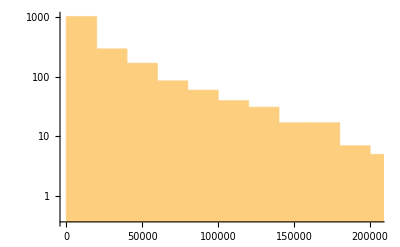

```mathematica
Length[names]
Histogram[FileByteCount/@names,100,ScalingFunctions->"Log"]
```

```mathematica
CodeInspector`Private`$Debug=xTrue;
CodeInspector`Report`Private`$Debug=xTrue;
CodeInspector`Format`Private`$Debug=xTrue;
$DebugLoop=xTrue;
$visuals=xTrue;
CodeInspector`Format`$Interactive=xTrue;
CodeInspector`Format`$NewLintStyle=True;
CodeInspector`Report`$Underlight=xTrue;
```

```mathematica
severityExclusions:={"Formatting","Remark"};
severityExclusions:={"Formatting"};
severityExclusions:={"Formatting","Remark","Warning","Error"};
severityExclusions:={"Formatting","Remark"};
severityExclusions={"Formatting","Remark"};
```

```mathematica
performanceGoal="Speed";
```

```mathematica
tagExclusions:=CodeInspector`Report`$DefaultTagExclusions~Join~{"UnusedVariables","UnusedBlockVariables",
"NotContiguous","StrayLineContinuation","UndocumentedCharacter","ObsoleteSymbol","ExperimentalSymbol"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","DuplicateClauses"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","TopLevel","Blank","ImplicitTimesStrings","DuplicateClauses","PostfixDifferentLine","UnexpectedCharacter","MissingFunction","SystemPatternBlank","DifferentLine"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","TopLevel","Blank","ImplicitTimesStrings","DuplicateClauses","PostfixDifferentLine","UnexpectedCharacter","MissingFunction","SystemPatternBlank","DifferentLine","LogicalConstant","WithArguments","UnexpectedSemicolon","ImplicitTimesBlanks","PrefixPlus","ExpectedSymbol","SuspiciousPrivateContext","SuspiciousRuleFunction","SuspiciousPatternBlankOptional","DotDifferentLine","StrangeCall"};
tagExclusions:={"ExperimentalSymbol","ObsoleteSymbol","UndocumentedSymbol","UnusedVariables","UnusedBlockVariables","ModuleArgumentsEmpty","WithArgumentsEmpty","LogicalConstant","CallDifferentLine","DuplicateKeys","DuplicateClauses","InfixBinaryAtQuirk","BlockArgumentsEmpty"};
tagExclusions:={"UnusedVariables","UnusedBlockVariables","ModuleArgumentsEmpty","WithArgumentsEmpty","DuplicateKeys","DuplicateClauses","BlockArgumentsEmpty","MissingFunction"};
tagExclusions={"UnusedVariables"};
```

```mathematica
CodeInspector`Report`Private`$ConfidenceLevel=1.0;
CodeInspector`Report`Private`$MaxConfidenceLevel=1.0;
```

```mathematica
CodeInspector`Private`$fileByteCountMinLimit=0.00*^6;
CodeInspector`Private`$fileByteCountMaxLimit=4.0*^6;
```

```mathematica
CodeInspector`External`$Editor="Sublime Text";
```

```mathematica
$ProcessID
```

17467

```mathematica
start=1;
```

```mathematica
x=start;
file=None;
Print["Linting ", Length[names[[start;;]]]," files"];
Print["Current file: ",Dynamic[Short[file]]];
Print["Current file size: ",Dynamic[FileSize[file]]];
Print["Current index: ",Dynamic[x]];
If[$visuals,
Print[Grid[{
{"concrete parse",Dynamic[CodeParser`Library`$ConcreteParseTime],ProgressIndicator[Dynamic[CodeParser`Library`$ConcreteParseProgress],{0,100}]},
{"aggregate parse",Dynamic[CodeParser`Abstract`$AggregateParseTime],ProgressIndicator[Dynamic[CodeParser`Abstract`$AggregateParseProgress],{0,100}]},
{"abstract parse",Dynamic[CodeParser`Abstract`$AbstractParseTime],ProgressIndicator[Dynamic[CodeParser`Abstract`$AbstractParseProgress],{0,100}]},
{"concrete lint",Dynamic[CodeInspector`$ConcreteLintTime],ProgressIndicator[Dynamic[CodeInspector`$ConcreteLintProgress],{0,100}]},
{"aggregate lint",Dynamic[CodeInspector`$AggregateLintTime],ProgressIndicator[Dynamic[CodeInspector`$AggregateLintProgress],{0,100}]},
{"abstract lint",Dynamic[CodeInspector`$AbstractLintTime],ProgressIndicator[Dynamic[CodeInspector`$AbstractLintProgress],{0,100}]},
{"","",Dynamic[PieChart[{CodeParser`Library`$ConcreteParseTime,CodeParser`Abstract`$AggregateParseTime,CodeParser`Abstract`$AbstractParseTime,CodeInspector`$ConcreteLintTime,CodeInspector`$AggregateLintTime,CodeInspector`$AbstractLintTime},ImageSize->Tiny,ChartLegends->{"concrete parse","aggregate parse","abstract parse","concrete lint","aggregate lint","abstract lint"}]]}
},Alignment->Right]];
];
Print[Row[{"overall",Spacer[10],ProgressIndicator[Dynamic[x],{0,Length[names]}]}]];
Scan[(
file=#;

Which[
TrueQ[$DebugLoop],
Print[x," ",file]
,
Mod[x,100]==0,
Print[x," ",file];
NotebookSave[EvaluationNotebook[]]
];

CodeParser`Library`$ConcreteParseProgress=0;
CodeParser`Abstract`$AggregateParseProgress=0;
CodeParser`Abstract`$AbstractParseProgress=0;
CodeInspector`$ConcreteLintProgress=0;
CodeInspector`$AggregateLintProgress=0;
CodeInspector`$AbstractLintProgress=0;
CodeParser`Library`$ConcreteParseTime=Quantity[0,"Seconds"];
CodeParser`Abstract`$AggregateParseTime=Quantity[0,"Seconds"];
CodeParser`Abstract`$AbstractParseTime=Quantity[0,"Seconds"];
CodeInspector`$ConcreteLintTime=Quantity[0,"Seconds"];
CodeInspector`$AggregateLintTime=Quantity[0,"Seconds"];
CodeInspector`$AbstractLintTime=Quantity[0,"Seconds"];
(*res=lintTest[file,x,"FileNamePrefixPattern"->prefix];*)
(*res=implicitTimesTest[file,x,"FileNamePrefixPattern"->prefix];*)
res=lintTest[file,x,"FileNamePrefixPattern"->prefix][file,x,"FileNamePrefixPattern"->prefix];
If[res=!=ok&&$visuals,
Pause[2.0];
];
x++;
)&
,
names[[start;;]]
]//AbsoluteTiming
```

Linting 1810 files

Current file:

Current file size:

Current index:

overall

index: 13 Algebra/TrigToRadicals.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Algebra/TrigToRadicals.m
 |  | 
line 197: |  |   |   |   |   |   |   |   | a | u | x | v | e | c |   | = |   | a | u | x | v | e | c |   | / | . |   | R | O | U | [ | c | , |   | 1 | ] | ^ | n | _ |   | - | > |   | R | O | U | [ | c | , |   | 1 | ] | ^ | M | o | d | [ | n | , |   | c | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 199: |  |   |   |   |   |   |   |   | a | u | x | v | e | c |   | = |   | a | u | x | v | e | c |   | / | / | . |   | R | O | U | [ | c | , |   | 1 | ] | ^ | n | _ |   | - | > |   | R | O | U | [ | c | , |   | 1 | ] | ^ | M | o | d | [ | n | , |   | c | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 252: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | r | p | e |   | = |   | r | p | e |   | / | . |   | R | O | U | [ | c | , |   | 1 | ] | ^ | n | _ |   | - | > |   | R | O | U | [ | c | , |   | 1 | ] | ^ | M | o | d | [ | n | , |   | c | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 23 Astronomy/PlanetaryAstronomy.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Astronomy/PlanetaryAstronomy.m
 |  | 
line 810: |  |   | P | A | T | r | a | n | s | f | o | r | m | a | t | i | o | n | 0 | [ | { | j | d | _ | , |   | p | _ | } | , |   | { | " | E | a | r | t | h | E | q | u | a | t | o | r | i | a | l | A | p | p | a | r | e | n | t | T | o | p | o | " | , |   | { | l | o | n | g | _ | , |   | l | a | t | _ | , |   | e | l | m | _ | } | } |   | - | > |   | { | " | E | a | r | t | h | A | p | p | a | r | e | n | t | " | , |   | { | l | o | n | g | _ | , |   | l | a | t | _ | , |   | e | l
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator]
m | _ | } | } | ] |   | : | = |   | { | j | d | , |   | E | q | u | a | t | o | r | i | a | l | T | o | H | o | r | i | z | o | n | X | [ | j | d | , |   | p | , |   | { | l | o | n | g | , |   | l | a | t | } | ] | } |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
\[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 811: |  |   | P | A | T | r | a | n | s | f | o | r | m | a | t | i | o | n | 0 | [ | { | j | d | _ | , |   | p | _ | } | , |   | { | " | E | a | r | t | h | A | p | p | a | r | e | n | t | " | , |   | { | l | o | n | g | _ | , |   | l | a | t | _ | , |   | e | l | m | _ | } | } |   | - | > |   | { | " | E | a | r | t | h | E | q | u | a | t | o | r | i | a | l | A | p | p | a | r | e | n | t | T | o | p | o | " | , |   | { | l | o | n | g | _ | , |   | l | a | t | _ | , |   | e | l
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator]
m | _ | } | } | ] |   | : | = |   | { | j | d | , |   | H | o | r | i | z | o | n | T | o | E | q | u | a | t | o | r | i | a | l | X | [ | j | d | , |   | p | , |   | { | l | o | n | g | , |   | l | a | t | } | ] | } |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
\[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 25 Asymptotics/AsymptoticDSolveValue.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Asymptotics/AsymptoticDSolveValue.m
 |  | 
line 319: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | D | e | r | i | v | a | t | i | v | e | [ | m | _ | ] | [ | y | ] | [ | - | I | n | f | i | n | i | t | y | ] | - | > |   | ( | - | 1 | ) | ^ | m | * | D | e | r | i | v | a | t | i | v | e | [ | m | ] | [ | z | ] | [ | I | n | f | i | n | i | t | y | ] | } | ] | ; |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 846: |  |   |   |   |   |   |   |   | b | c | s | 1 |   | = |   | Q | u | i | e | t | [ | b | c | s | 1 |   | / | . |   | { | w | [ | p | _ | ] | [ | I | n | f | i | n | i | t | y | ] | - | > | z | [ | p | ] | [ | 0 | ] | , |   | D | e | r | i | v | a | t | i | v | e | [ | m | _ | ] | [ | w | [ | p | _ | ] | ] | [ | I | n | f | i | n | i | t | y | ] | - | > |   | 0 | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 28 Asymptotics/AsymptoticProduct.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Asymptotics/AsymptoticProduct.m
 |  | 
line 442: |  |   | U | n | i | v | a | r | i | a | t | e | F | i | n | i | t | e | B | i | r | k | h | o | f | f | P | r | o | d | u | c | t | [ | f | _ | , |   | { | k | _ | , |   | a | _ | , |   | m | _ | + | b | _ | . | } | , |   | { | m | _ | , |   | I | n | f | i | n | i | t | y | _ | , |   | n | _ | } | ] | / | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  |

index: 30 Asymptotics/AsymptoticRSolveValue.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Asymptotics/AsymptoticRSolveValue.m
 |  | 
line 680: |  |   |   |   |   |   |   |   |   |   |   |   |   | b | c | s | 1 |   | = |   | ( | b | c | s |   | / | . |   | T | a | b | l | e | [ | y | [ | [ | i | ] | ] | [ | p | _ | ] | - | > |   | y | 1 | [ | p | ] | [ | [ | i | ] | ] | , |   | { | i | , |   | L | e | n | g | t | h | [ | y | ] | } | ] | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 31 Asymptotics/AsymptoticSolve.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Asymptotics/AsymptoticSolve.m
 |  | 
line 170: |  |   | $ | s | i | m | p | e | x | p | l | o | g | r | u | l | e |   | = |   | { | R | e | d | u | c | e | ` | I | n | e | r | t | E | x | p | [ | R | e | d | u | c | e | ` | I | n | e | r | t | L | o | g | [ | e | _ | ] | ] | - | > | e | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 33 Asymptotics/AsymptoticsUtils.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Asymptotics/AsymptoticsUtils.m
 |  | 
line 615: |  |   |   |   |   |   |   |   | a | n | s | = | { | u | , |   | m | , |   | u | u | , |   | v | v | } | / | . | W | [ | F | u | n | c | t | i | o | n | [ | e | _ | ] | ] | - | > | e | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 860: |  |   |   |   |   |   |   |   |   |   |   | { | s | , |   | w | w | } | = | ( | { | s | , |   | w | w | } | / | . | r | r | ) | / | / | . | R | e | d | u | c | e | ` | I | n | e | r | t | E | x | p | [ | R | e | d | u | c | e | ` | I | n | e | r | t | L | o | g | [ | u | _ | ] | ] | - | > | u | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 36 Asymptotics/DiscreteMaxLimit.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Asymptotics/DiscreteMaxLimit.m
 |  | 
line 610: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | ( | f |   | / | . |   | { | F | a | c | t | o | r | i | a | l | P | o | w | e | r | [ | a | _ | , |   | b | _ | ] |   | / | ; |   | ! | F | r | e | e | Q | [ | { | a | , | b | } | , |   | n | ] |   | - | > |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
line 611: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   |   | F | u | n | c | t | i | o | n | E | x | p | a | n | d | [ | F | a | c | t | o | r | i | a | l | P | o | w | e | r | [ | a | , |   | b | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 38 Asymptotics/GLimit.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Asymptotics/GLimit.m
 |  | 
line  999: |  |   |   |   |   |   |   |   | e | e | = | e | / | . | { | C | o | s | [ | t | _ | ] |   | - | > |   | c | o | s | [ | t | ] | , |   | S | e | c | [ | t | _ | ] |   | - | > |   | 1 | / | c | o | s | [ | t | ] | , |   | T | a | n | [ | t | _ | ] |   | - | > |   | s | i | n | [ | t | ] | / | c | o | s | [ | t | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1000: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   | S | i | n | [ | t | _ | ] |   | - | > |   | s | i | n | [ | t | ] | , |   | C | s | c | [ | t | _ | ] |   | - | > |   | 1 | / | s | i | n | [ | t | ] | , |   | C | o | t | [ | t | _ | ] |   | - | > |   | c | o | s | [ | t | ] | / | s | i | n | [ | t | ] | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 40 Asymptotics/MultivariateLimit.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Asymptotics/MultivariateLimit.m
 |  | 
line 1625: |  |   |   |   |   |   |   |   | f | f | = | f | / | . | { | S | i | n | [ | e | _ | ] |   | - | > |   | S | I | N | [ | e | ] | , |   | C | o | s | [ | e | _ | ] | - | > | C | O | S | [ | e | ] | , |   | T | a | n | [ | e | _ | ] | - | > | S | I | N | [ | e | ] | / | C | O | S | [ | e | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1626: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   | C | s | c | [ | e | _ | ] |   | - | > |   | 1 | / | S | I | N | [ | e | ] | , |   | S | e | c | [ | e | _ | ] | - | > | 1 | / | C | O | S | [ | e | ] | , |   | C | o | t | [ | e | _ | ] | - | > | C | O | S | [ | e | ] | / | S | I | N | [ | e | ] | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1941: |  |   |   |   |   |   |   |   |   |   |   | f | f | = | f | f | / | . | A | b | s | [ | e | 1 | _ | ] |   | A | b | s | [ | e | 2 | _ | ] | - | > | A | b | s | [ | e | 1 |   | e | 2 | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1942: |  |   |   |   |   |   |   |   |   |   |   | f | f | = | f | f | / | . | A | b | s | [ | e | _ | ? | A | R | e | a | l | I | f | D | e | f | i | n | e | d | Q | ] | - | > | S | q | r | t | [ | e | ^ | 2 | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2158: |  |   |   |   |   |   |   |   |   |   |   | f | s | = | R | e | p | l | a | c | e | [ | # | , |   | { | P | o | w | e | r | [ | a | _ | , |   | _ | R | a | t | i | o | n | a | l | ] | - | > | a | , |   | A | b | s | [ | a | _ | ] | - | > | a | } | ] | & | / | @ | f | s | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2204: |  |   |   |   |   |   |   |   |   |   |   | l | i | m | = | l | i | m | / | . | G | L | i | m | i | t | I | n | t | e | r | v | a | l | [ | a | _ | , |   | b | _ | , |   | _ | ] | - | > | I | n | t | e | r | v | a | l | [ | { | a | , |   | b | } | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2255: |  |   |   |   |   |   |   |   |   |   |   | l | i | m | = | l | i | m | / | . | G | L | i | m | i | t | I | n | t | e | r | v | a | l | [ | a | _ | , |   | b | _ | , |   | _ | ] | - | > | I | n | t | e | r | v | a | l | [ | { | a | , |   | b | } | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2364: |  |   |   |   |   |   |   |   | { | f | 0 | , |   | f | f | } | = | { | f | 0 | , |   | f | f | } | / | . | S | i | n | [ | e | _ | ? | ( | ! | F | r | e | e | Q | [ | # | , |   | T | ] | & | ) | ] | ^ | ( | k | _ | ? | E | v | e | n | Q | ) | - | > | ( | 1 | - | C | o | s | [ | e | ] | ^ | 2 | ) | ^ | ( | k | / | 2 | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2535: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | A | b | s | [ | e | _ | ] | ^ | k | _ |   | / | ; |   | M | e | m | b | e | r | Q | [ | r | v | , |   | e | ] |   | & | & |   | E | v | e | n | Q | [ | k | ] |   | - | > |   | e | ^ | k | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 47 Audio/Internals/GUIVisualization.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Audio/Internals/GUIVisualization.m
 |  | 
line 246: |  |   |   |   | 1 |   | ; | ; |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] |  
Operands for ;; are on different lines.11814689Delimiter
 |  | 
 |  | 
line 247: |  |   |   |   | M | i | n | [ | d | a | t | a | L | e | n | , |   | R | o | u | n | d | [ | s | a | m | p | l | e | R | a | t | e | * | O | p | t | i | o | n | V | a | l | u | e | [ | " | V | i | z | T | i | m | e | " | ] | ] | ] |   | ; | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] |  
Operands for ;; are on different lines.11814689Delimiter
 |  |

index: 52 Audio/Processing/Editing.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Audio/Processing/Editing.m
 |  | 
line  67: |  |   |   |   | i | n | t | e | r | v | a | l | s |   | = |   | C | l | i | p | [ | L | i | s | t | @ | @ | I | n | t | e | r | v | a | l | [ | i | n | t | e | r | v | a | l | s | / | . |   | x | _ |   | / | ; |   | x |   | < |   | 0 |   | - | > |   | d | u | r | + | x | ] | , | { | 0 | , | d | u | r | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  76: |  |   |   |   | i | n | t | e | r | v | a | l | s |   | = |   | C | l | i | p | [ | L | i | s | t | @ | @ | ( | I | n | t | e | r | v | a | l | U | n | i | o | n | [ | S | e | q | u | e | n | c | e | @ | @ | ( | I | n | t | e | r | v | a | l | / | @ | ( | i | n | t | e | r | v | a | l | s | / | . |   | x | _ |   | / | ; |   | x |   | < |   | 0 |   | - | > |   | d | u | r | + | x | ) | ) | ] | ) | , | { | 0 | , | d | u | r | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 139: |  |   |   | s | p | l | i | t | P | o | i | n | t | s |   | = |   | D | e | l | e | t | e | D | u | p | l | i | c | a | t | e | s | @ | D | e | l | e | t | e | C | a | s | e | s | [ | S | o | r | t | [ | s | p | l | i | t | P | o | i | n | t | s |   | / | . |   | x | _ |   | / | ; |   | x |   | < |   | 0 |   | - | > |   | d | u | r |   | + |   | x | ] | , |   | x | _ |   | / | ; |   | x |   | = | = | = |   | 0 | . |   | | | | |   | x |   | = | = | = |   | d | u | r | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 53 Audio/Processing/Effects.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Audio/Processing/Effects.m
 |  | 
line  268: |  |   |   |   | h | i | c | u | t |   | = |   | A | u | d | i | o | ` | U | t | i | l | i | t | i | e | s | ` | G | e | t | F | r | e | q | u | e | n | c | y | [ | m | e | t | h | o | d | / | . | ( | { | " | L | o | w | p | a | s | s | C | u | t | o | f | f | " |   | - | > |   | x | _ | } | ) |   | - | > |   | x | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  673: |  |   |   |   |   |   |   | { | y | _ | ? | ( | M | a | t | c | h | Q | [ | # | , | " | S | t | e | r | e | o | " | ] | & | ) | , | A | u | t | o | m | a | t | i | c | , | A | u | t | o | m | a | t | i | c | } | - | > | y | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  674: |  |   |   |   |   |   |   | { | A | u | t | o | m | a | t | i | c | , | x | _ | ? | ( | A | r | r | a | y | D | e | p | t | h | [ | # | ] | = | = | 1 | & | ) | } | - | > | { | " | S | t | e | r | e | o | " | , | x | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  675: |  |   |   |   |   |   |   | { | A | u | t | o | m | a | t | i | c | , | x | _ | ? | ( | A | r | r | a | y | D | e | p | t | h | [ | # | ] | = | = | 2 | & | ) | } | - | > | { | 2 | , | x | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  676: |  |   |   |   |   |   |   | { | x | _ | , | A | u | t | o | m | a | t | i | c | } | - | > | x | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  677: |  |   |   |   |   |   |   | { | A | u | t | o | m | a | t | i | c | , | y | _ | , | A | u | t | o | m | a | t | i | c | } | - | > | { | " | S | t | e | r | e | o | " | , | y | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  678: |  |   |   |   |   |   |   | { | A | u | t | o | m | a | t | i | c | , | x | _ | , | y | _ | } | - | > | { | " | S | t | e | r | e | o | " | , | x | , | y | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  679: |  |   |   |   |   |   |   | { | x | _ | ? | ( | M | a | t | c | h | Q | [ | # | , | " | S | t | e | r | e | o | " | ] | & | ) | , | A | u | t | o | m | a | t | i | c | , | y | _ | } | - | > | { | x | , | C | o | n | s | t | a | n | t | A | r | r | a | y | [ | 1 | . | / | i | n | c | h | a | n | n | e | l | s | , | i | n | c | h | a | n | n | e | l | s | ] | , | y | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  680: |  |   |   |   |   |   |   | { | x | _ | ? | ( | M | a | t | c | h | Q | [ | # | , | " | S | t | e | r | e | o | " | ] | & | ) | , | y | _ | , | A | u | t | o | m | a | t | i | c | } | - | > | { | x | , | y | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1247: |  |   | a | l | l | p | a | s | s | f | r | e | e | [ | g | _ | , | N | _ | ] |   | : | = |   | ( | - |   | 1 |   | + |   | ( | 1 |   | + |   | g | ) | * | z | ^ | - | N | ) | / | ( | 1 |   | - |   | g | * | z | ^ | - | N | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line 1248: |  |   | l | b | c | f | [ | f | _ | , | d | _ | , | N | _ | ] |   | : | = |   | z | ^ | - | N | / | ( | 1 |   | - |   | f | * | ( | ( | 1 |   | - |   | d | ) | / | ( | 1 |   | - |   | d | * | z | ^ | - | 1 | ) | ) | * | z | ^ | - | N | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  |

index: 71 Audio/Utilities/Utilities.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Audio/Utilities/Utilities.m
 |  | 
line 109: |  |   |   | { | a |   | = |   | A | u | d | i | o | ` | U | t | i | l | i | t | i | e | s | ` | G | e | t | T | i | m | e | [ | x | / | . | { | S | c | a | l | e | d | [ | d | _ | ] | - | > | d | * | l | e | n | g | t | h | , | N | o | n | e | - | > | 0 | . | } | , | s | ] | , | p | a | d | S | i | z | e | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 133: |  |   |   | { | a |   | = |   | A | u | d | i | o | ` | U | t | i | l | i | t | i | e | s | ` | G | e | t | S | a | m | p | l | e | s | [ | x | / | . | { | S | c | a | l | e | d | [ | d | _ | ] | - | > | d | * | d | u | r | , | N | o | n | e | - | > | 0 | . | } | , | s | r | ] | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 73 Audio/Visualization/Visualization.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Audio/Visualization/Visualization.m
 |  | 
line 553: |  |   |   |   | p | p | a | d | d | i | n | g | [ | [ | 1 | ] | ] | / | . | { | A | u | t | o | m | a | t | i | c | - | > | A | b | s | @ | ( | p | r | a | n | g | e | [ | [ | 1 | , | 2 | ] | ] | - | p | r | a | n | g | e | [ | [ | 1 | , | 1 | ] | ] | ) | * | . | 0 | 1 | , |   | N | o | n | e | - | > | 0 | , |   | S | c | a | l | e | d | [ | x | _ | ] | - | > | A | b | s | @ | ( | p | r | a | n | g | e | [ | [ | 1 | , | 2 | ] | ] | - | p | r | a | n | g | e | [ | [ | 1 | , | 1
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
] | ] | ) | * | x | } | , |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 554: |  |   |   |   | p | p | a | d | d | i | n | g | [ | [ | 2 | ] | ] | / | . | { | A | u | t | o | m | a | t | i | c | - | > | A | b | s | @ | ( | p | r | a | n | g | e | [ | [ | 2 | , | 2 | ] | ] | - | p | r | a | n | g | e | [ | [ | 2 | , | 1 | ] | ] | ) | * | . | 0 | 5 | , |   | N | o | n | e | - | > | 0 | , |   | S | c | a | l | e | d | [ | x | _ | ] | - | > | A | b | s | @ | ( | p | r | a | n | g | e | [ | [ | 2 | , | 2 | ] | ] | - | p | r | a | n | g | e | [ | [ | 2 | , | 1
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
] | ] | ) | * | x | } |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 986: |  |   |   | r | e | s |   | = |   | Q | u | i | e | t | @ | { | R | e | p | l | a | c | e | [ | r | e | s | [ | [ | 1 | ] | ] | , |   | x | _ |   | / | ; |   | c | h | e | c | k | F | t | i | c | k | s | [ | x | @ | @ | p | r | a | n | g | e | [ | [ | 2 | ] | ] | ] | - | > | x | @ | @ | p | r | a | n | g | e | [ | [ | 2 | ] | ] | , | 2 | ] | , | R | e | p | l | a | c | e | [ | r | e | s | [ | [ | 2 | ] | ] | , |   | x | _ |   | / | ; |   | c | h | e | c | k | F | t | i | c | k
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
s | [ | x | @ | @ | p | r | a | n | g | e | [ | [ | 1 | ] | ] | ] | - | > | x | @ | @ | p | r | a | n | g | e | [ | [ | 1 | ] | ] | , | 2 | ] | } | ; |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 90 CharacterFunctions/Transliterate.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/CharacterFunctions/Transliterate.m
 |  | 
line 83: |  |   | i | T | r | a | n | s | l | i | t | e | r | a | t | e | 1 | [ | { | t | e | x | t | _ | S | t | r | i | n | g | ? | S | t | r | i | n | g | Q | , |   | R | u | l | e | [ | x | _ | , | x | _ | ] | } | , |   | v | a | r | i | a | n | t | _ | ] |   | : | = |   | t | e | x | t |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 91 CompileDefinition.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/CompileDefinition.m
 |  | 
line 502: |  |   |   |   |   |   |   | s | u | b | s | t |   | = |   | M | a | p | [ | R | e | p | l | a | c | e | [ | # | , |   | ( | a | _ |   | : | > |   | H | o | l | d | C | o | m | p | l | e | t | e | [ | b | _ | ] | ) |   | - | > |   | a |   | : | > |   | b | ] |   | & | , |   | s | u | b | s | t | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 94 Control/AffineModelAnalysis.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Control/AffineModelAnalysis.m
 |  | 
line 925: |  |   | o | p | g | T | o | 0 | [ | H | o | l | d | P | a | t | t | e | r | n | [ | R | u | l | e | [ | x | _ | , |   | x | _ | ] | ] | ] | : | = |   | R | u | l | e | [ | x | , |   | 0 | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 99 Control/Common.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Control/Common.m
 |  | 
line  473: |  |   | p | r | e | c | i | s | i | o | n |   | = |   | I | n | t | e | r | n | a | l | ` | E | f | f | e | c | t | i | v | e | P | r | e | c | i | s | i | o | n | [ | # |   | / | / | . |   | _ | S | y | m | b | o | l | [ | a | r | g | s | _ | _ | _ | ] | - | > | { | a | r | g | s | } | ] | & |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  736: |  |   |   |   |   |   | I | f | [ |   | F | a | l | s | e |   | & | & |   | ! | p | z | e | r | o | Q | [ | p | r | , | v | a | r | , | 0 | ] |   | & | & |   | ! | p | z | e | r | o | Q | [ | p | q | c | h | , | v | a | r | , | 0 | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Logical constant in And.11814689Delimiter
 |  | 
 |  | 
line 5677: |  |   |   |   | ( | * | ] |   | * | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Operand for ; is on different line.11814689Delimiter
 |  |

100 /Users/brenton/development/stash/KERN/Kernel/StartUp/Control/CommonPatterns.m

index: 102 Control/Conversions.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Control/Conversions.m
 |  | 
line 429: |  |   |   |   |   |   | m | a | t | s |   | = |   | m | a | t | s |  
  | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: mats.11814689Delimiter
 |  |

index: 107 Control/NyquistNichols.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Control/NyquistNichols.m
 |  | 
line 1197: |  |   |   |   |   |   |   | I | n | t | e | r | v | a | l | M | e | m | b | e | r | Q | [ | I | n | t | e | r | v | a | l | [ | p | l | o | t | r | a | n | g | e | Y | ] | , |   | s | o | l | s | [ | [ | 1 | ] | ] | ] | , |   | x | C | r | o | s | s | i | n | g |   | = |   | x | C | r | o | s | s | i | n | g | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Self assignment: xCrossing.11814689Delimiter
 |  | 
 |  | 
line 1204: |  |   |   |   |   |   |   | I | n | t | e | r | v | a | l | M | e | m | b | e | r | Q | [ | I | n | t | e | r | v | a | l | [ | p | l | o | t | r | a | n | g | e | X | ] | , |   | s | o | l | s | [ | [ | 1 | ] | ] | ] | , |   | y | C | r | o | s | s | i | n | g |   | = |   | y | C | r | o | s | s | i | n | g | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Self assignment: yCrossing.11814689Delimiter
 |  |

index: 111 Control/PIDRules.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Control/PIDRules.m
 |  | 
line 2262: |  |   |   |   |   |   |   |   |   |   | S | i | m | p | l | i | f | y | @ | T | r | a | n | s | f | e | r | F | u | n | c | t | i | o | n | M | o | d | e | l | [ | n | u | m | d | e | n | / | . |   | E | ^ | ( | a | r | g | _ | ) |   | - | > |   | P | a | d | e | A | p | p | r | o | x | i | m | a | n | t | [ | E | x | p | [ | a | r | g | ] | , |   | { | a | r | g | , |   | 0 | , |   | { | 2 | , |   | 2 | } | } | ] | , | v | a | r | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2472: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | t | s | e | t |   | = |   | t | s | e | t | ; | ( | * | g | e | t | S | e | t | t | l | i | n | g | T | i | m | e | [ | p | t | s | , |   | A | b | s | [ |   | R | e | v | e | r | s | e | [ | l | s | t | o | r | ] |   | - |   | 1 | ] | ] | ; | * | ) | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Self assignment: tset.11814689Delimiter
 |  |

index: 114 Control/PolynomialSmith.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Control/PolynomialSmith.m
 |  | 
line 536: |  |   |   |   |   | I | f | [ | F | a | l | s | e |   | & | & |   | a | p | p | r | o | x | , | ( | * | e | x | p | e | r | i | m | e | n | t | a | l | ! | ! | ! | * | ) |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Logical constant in And.11814689Delimiter
 |  | 
 |  | 
line 674: |  |   |   |   |   | I | f | [ | F | a | l | s | e |   | & | & |   | a | p | p | r | o | x | , | ( | * | e | x | p | e | r | i | m | e | n | t | a | l | ! | ! | ! | * | ) |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Logical constant in And.11814689Delimiter
 |  |

index: 119 Control/Simulations.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Control/Simulations.m
 |  | 
line 558: |  |   |   |   |   | [ | s | t | a | t | e | r | e | s | p | o | n | s | e | , | p | a | r | s | e | d | , | i | n | i | t | s | , | u | , | t | , | e | x | a | c | t | Q | , | o | p | t | s | ] | , |  
  | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Call is on different lines.11814689Delimiter
 |  |

index: 124 Convert/AffymetrixCDF.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/AffymetrixCDF.m
 |  | 
line 240: |  |   | A | S | C | I | I | B | l | o | c | k | R | e | a | d | e | r | [ | s | t | r | m | _ | , |   | V | e | r | s | i | o | n | _ | , |   | U | n | i | t | T | y | p | e | _ | ] | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  |

index: 126 Convert/AffymetrixCHP.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/AffymetrixCHP.m
 |  | 
line 161: |  |   |   |   |   |   |   |   |   |   |   | S | t | r | i | n | g | S | p | l | i | t | [ | # | ~ | ~ | " | N | o | n | e | " | , | " | = | " | ] | / | . | { | a | _ | , | b | _ | } | - | > |   | R | u | l | e | [ | a | , | T | o | E | x | p | r | e | s | s | i | o | n | [ | b | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 162: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | S | t | r | i | n | g | S | p | l | i | t | [ | # | , | " | = | " | ] | / | . | { | a | _ | , | b | _ | } | - | > |   | R | u | l | e | [ | a | , | T | o | E | x | p | r | e | s | s | i | o | n | [ | b | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 181: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | M | a | p | [ | F | u | n | c | t | i | o | n | [ | S | t | r | i | n | g | S | p | l | i | t | [ | # | , | " | : | " | ] | / | . | { | a | _ | , | b | _ | } | - | > |   | R | u | l | e | [ | a | , | E | v | a | l | u | a | t | e | [ | b | ] | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 187: |  |   |   |   |   |   |   | M | a | p | [ | S | t | r | i | n | g | S | p | l | i | t | [ | # | , | " | = | " | ] | / | . | { | a | _ | , | b | _ | } | - | > |   | R | u | l | e | [ | a | , | b | ] | & | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 440: |  |   |   | o | u | t |   | / | . |   | { | a | _ | , | b | _ | , | c | _ | , | d | _ | , | e | _ | , | f | _ | , | g | _ | , | h | _ | , | i | _ | , | j | _ | , | k | _ | , | l | _ | , | m | _ | , | n | _ | , | o | _ | } | - | > |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
line 441: |  |   |   |   |   |   |   |   |   |   | { | a | / | 1 | 0 | 0 | 0 | , | b | , | c | , | d | / | 1 | 0 | 0 | 0 | , | e | / | 1 | 0 | 0 | 0 | , | f | , | g | , | h | , | i | , | j | , | k | / | 1 | 0 | 0 | 0 | , | l | / | 1 | 0 | 0 | 0 | , | m | , | n | , | o | } |   |   |   |   |   |   |   |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 129 Convert/AffymetrixPSI.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/AffymetrixPSI.m
 |  | 
line 30: |  |   |   |   | [ |   | { | " | D | a | t | a | " |   | - | > |   | { |   | s |   | - | > |   |  
  | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Call is on different lines.11814689Delimiter
 |  | 
 |  | 
line 47: |  |   |   |   | [ |   | { | " | D | a | t | a | " |   | - | > |   | { |   | i |   | - | > |   |  
  | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Call is on different lines.11814689Delimiter
 |  |

index: 130 Convert/AgilentMicroarray.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/AgilentMicroarray.m
 |  | 
line 88: |  |   |   | d | a | t | a | = | S | y | s | t | e | m | ` | C | o | n | v | e | r | t | ` | T | a | b | l | e | D | u | m | p | ` | P | a | r | s | e | T | a | b | l | e | [ | d | a | t | a | , | { | { | { | " | \ | : | 0 | 0 | 0 | 1 | " | } | , |   | { | " | \ | : | 0 | 0 | 0 | 1 | " | } | } | , | { | " | - | " | , |   | " | + | " | } | , | " | . | " | } | , | F | a | l | s | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:0001.11814689Delimiter
Unexpected character: \:0001.11814689Delimiter
 |  |

index: 135 Convert/BDF.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/BDF.m
 |  | 
line 237: |  |   |   |   | l | s | t |   | = |   | l | s | t |   | / | . | s | _ | S | t | r | i | n | g | - | > | d | e | l | e | t | e | W | h | i | t | e | S | p | a | c | e | s | [ | s | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 255: |  |   |   |   | l | s | t |   | = |   | l | s | t |   | / | . | s | _ | S | t | r | i | n | g | - | > | d | e | l | e | t | e | W | h | i | t | e | S | p | a | c | e | s | [ | s | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 138 Convert/BYU.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/BYU.m
 |  | 
line 144: |  |   |   | p | o | l | y | s |   | = |   | M | a | p | [ | R | e | p | l | a | c | e | [ | # | , |   | { | a | _ | _ | , |   | b | _ | } |   | - | > |   | { | a | , |   | - | b | } | ] |   | & | , |   | # | , |   | 2 | ] | & |   | / | @ |   | p | o | l | y | s | ; |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 148 Convert/Common3D.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/Common3D.m
 |  | 
line  933: |  |   |   |   |   |   |   | f | i | n | a | l | c | o | l | o | r |   | = |   | n | e | w | c | o | l | o | r | / | . | R | G | B | C | o | l | o | r | [ | p | _ | , | q | _ | , | r | _ | ] | - | > | R | G | B | C | o | l | o | r | [ | p | , | q | , | r | , | o | p | a | c | i | t | y | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  957: |  |   |   |   |   |   |   | f | i | n | a | l | c | o | l | o | r |   | = |   | n | e | w | c | o | l | o | r | / | . | R | G | B | C | o | l | o | r | [ | p | _ | , | q | _ | , | r | _ | ] | - | > | R | G | B | C | o | l | o | r | [ | p | , | q | , | r | , | o | p | a | c | i | t | y | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1585: |  |   |   |   | c | o | l | o | r | s |   | = |   | c | o | l | o | r | s | / | . | R | G | B | C | o | l | o | r | [ | p | _ | , | q | _ | , | r | _ | ] | - | > | R | G | B | C | o | l | o | r | [ | p | , | q | , | r | , | o | p | a | c | i | t | y | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1588: |  |   |   | c | o | l | o | r | s |   | = |   | c | o | l | o | r | s | / | . | R | G | B | C | o | l | o | r | [ | p | _ | ? | N | u | m | b | e | r | Q | , | q | _ | ? | N | u | m | b | e | r | Q | , | r | _ | ? | N | u | m | b | e | r | Q | ] | - | > | R | G | B | C | o | l | o | r | [ | p | , | q | , | r | , | o | p | a | c | i | t | y | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1698: |  |   |   |   |   |   | r | u | l | e | s | 1 |   | = |   | r | u | l | e | s | / | . |   | T | r | i | a | n | g | l | e | [ | a | _ | ] |   | - | > |   | P | o | l | y | g | o | n | [ | a | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1742: |  |   |   |   |   | g | r |   | = |   | C | a | s | e | s | [ | e | l | e | m | s | , |   | H | o | l | d | P | a | t | t | e | r | n | [ | " | G | r | a | p | h | i | c | s | 3 | D | " | | | " | G | r | a | p | h | i | c | s | " | - | > | v | a | l | u | e | _ | ] |   | - | > |   | v | a | l | u | e | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 149 Convert/CommonGraphics.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/CommonGraphics.m
 |  | 
line  301: |  |   |   |   |   | [ | M | a | n | i | p | u | l | a | t | e |   | @ | @ |   | J | o | i | n | [ |  
  | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Call is on different lines.11814689Delimiter
 |  | 
 |  | 
line  412: |  |   |   |   |   | [ |  
  | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Call is on different lines.11814689Delimiter
 |  | 
 |  | 
line  438: |  |   |   |   |   | [ |  
  | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Call is on different lines.11814689Delimiter
 |  | 
 |  | 
line  467: |  |   |   |   |   | [ |  
  | ␣ | ␣ | ␣ | \[ErrorIndicator] |  
Call is on different lines.11814689Delimiter
 |  | 
 |  | 
line 1171: |  |   |   | i | n | c | l | E | x | i | f |   | = |   | R | e | p | l | a | c | e | [ | i | n | c | l | u | d | e | M | e | t | a | I | n | f | o | r | m | a | t | i | o | n | , |   | { | ( | T | r | u | e |   | | |   | A | l | l |   | | |   | { | _ | _ | _ | , |   | " | e | x | i | f | " | , |   | _ | _ | _ | } | ) |   | - | > |   | T | r | u | e | , |   | ( | F | a | l | s | e |   | | |   | N | o | n | e |   | | |   | _ | ) |   | - | > |   | F | a | l | s | e | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 2726: |  |   |   |   |   | e | l | e | m | v | a | l | u | e |   | = |   | e | l | e | m | v | a | l | u | e |  
  | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Self assignment: elemvalue.11814689Delimiter
 |  |

index: 161 Convert/Dicom.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/Dicom.m
 |  | 
line 946: |  |   |   |   | c | h | a | r | s |   | = |   | c | h | a | r | s |   | / | / | . |   | { | " |   | " | , |   | r | e | s | t | _ | _ | _ | } |   | - | > |   | { | r | e | s | t | } |   | / | / | . |   | { | r | e | s | t | _ | _ | _ | , |   | " |   | " | } |   | - | > |   | { | r | e | s | t | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 165 Convert/DOT.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/DOT.m
 |  | 
line 776: |  |   |   |   |   |   | R | e | v | e | r | s | e | / | @ | D | e | l | e | t | e | C | a | s | e | s | [ | e | d | g | e | s | , |   | H | o | l | d | P | a | t | t | e | r | n | [ | R | u | l | e | [ | x | _ | , |   | x | _ | ] | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 167 Convert/DXF.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/DXF.m
 |  | 
line  319: |  |   |   | l | e | f | t | o | v | e | r | s |   | = |   | D | e | l | e | t | e | C | a | s | e | s | [ | n | e | w | g | r | , |   | P | o | l | y | g | o | n | [ | _ | _ | _ | ] |   | | |   | C | u | b | o | i | d | [ | _ | _ | _ | ] |   | | |   | S | p | h | e | r | e | [ | _ | _ | _ | ] |   | | |   | S | p | h | e | r | e | [ | _ | _ | _ | ] |   | | |   | C | y | l | i | n | d | e | r | [ | _ | _ | _ | ] |   | | |   | T | u | b | e | [ | _ | _ | _ | ] | , |   | I | n | f
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Duplicate clauses in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line  430: |  |   |   | v | e | r | t | s |   | = |   | R | e | p | l | a | c | e | A | l | l | [ | v | e | r | t | s | , |   | { | p | _ | ? | N | u | m | b | e | r | Q | , |   | q | _ | ? | N | u | m | b | e | r | Q | } |   | - | > |   | { | p | , |   | q | , |   | 0 | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  438: |  |   |   |   | v | c | o | l | s |   | = |   | ( | T | o | C | o | l | o | r | [ | # | , |   | R | G | B | C | o | l | o | r | ] | & |   | / | @ |   | v | c | o | l | s | ) | / | . | R | G | B | C | o | l | o | r | [ | p | _ | , | q | _ | , | r | _ | , | _ | _ | _ | ] | - | > | { | p | , | q | , | r | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  441: |  |   |   |   | p | o | l | y | c | o | l | s |   | = |   | { | M | a | p | [ | ( | T | o | t | a | l | [ | # | ] | / | L | e | n | g | t | h | @ | # | ) | / | . | L | i | s | t | [ | p | _ | , | q | _ | , | r | _ | ] | - | > | R | G | B | C | o | l | o | r | [ | p | , | q | , | r | ] | & | , |   | F | i | r | s | t | [ | p | o | l | y | c | o | l | s | ] | , |   | 1 | ] | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  518: |  |   |   | v | e | r | t | s |   | = |   | p | a | r | t | [ | [ | 2 | ] | ] | / | . | ( | P | o | l | y | g | o | n | [ | v | _ | , | _ | _ | _ | ] | - | > | v | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  519: |  |   |   | I | f | [ | L | e | n | g | t | h | @ | v | e | r | t | s |   | = | = | = |   | 3 | , |   | v | e | r | t | s |   | = |   | v | e | r | t | s | / | . | { | p | 1 | _ | , | p | 2 | _ | , | p | 3 | _ | } | - | > | { | p | 1 | , | p | 2 | , | p | 3 | , | p | 3 | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1169: |  |   |   | I | f | [ | F | r | e | e | Q | [ | D | e | l | e | t | e | C | a | s | e | s | [ | l | a | y | e | r | s | , |   | { | R | G | B | C | o | l | o | r | [ | 1 | , | 1 | , | 1 | ] | } |   | | |   | { | R | G | B | C | o | l | o | r | [ | 1 | , |   | 1 | , |   | 1 | ] | } |   | | |   | R | G | B | C | o | l | o | r | [ | 1 | . | , | 1 | . | , | 1 | . | ] |   | | |   | R | G | B | C | o | l | o | r | [ | 1 | . | , |   | 1 | . | , |   | 1 | . | ] | , |   | I | n | f | i
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Duplicate clauses in Alternatives.11180111146203218891Delimiter
 |  |

index: 168 Convert/EDF.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/EDF.m
 |  | 
line 185: |  |   |   |   | l | s | t |   | = |   | l | s | t |   | / | . | s | _ | S | t | r | i | n | g | - | > | d | e | l | e | t | e | W | h | i | t | e | S | p | a | c | e | s | [ | s | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 199: |  |   |   |   | l | s | t |   | = |   | l | s | t |   | / | . | s | _ | S | t | r | i | n | g | - | > | d | e | l | e | t | e | W | h | i | t | e | S | p | a | c | e | s | [ | s | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 173 Converters.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Converters.m
 |  | 
line  222: |  |   | d | r | o | p | e | x | t | [ | f | i | l | e | _ | S | t | r | i | n | g | ] |   | : | = |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | f | i | l | e | , |   | x | _ | _ |   | ~ | ~ |   | " | . | " |   | ~ | ~ |   | _ | _ |   | - | > |   | x | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2028: |  |   |   |   |   | _ | _ | _ |   | ~ | ~ |   | " | / | " |   | ~ | ~ |   | f | n | a | m | e | _ | _ |   | ~ | ~ |   | " | ? | " |   | ~ | ~ |   | q | u | e | r | y | _ | _ | _ |   | - | > |   | f | n | a | m | e | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2029: |  |   |   |   |   | _ | _ | _ |   | ~ | ~ |   | " | / | " |   | ~ | ~ |   | f | n | a | m | e | _ | _ |   | ~ | ~ |   | E | n | d | O | f | S | t | r | i | n | g |   | - | > |   | f | n | a | m | e | } |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 178 Convert/FBX.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/FBX.m
 |  | 
line 906: |  |   |   |   |   |   |   | p | o | i | n | t | s |   | = |   | C | a | s | e | s | [ | d | a | t | a | , |   | { | " | p | " | , |   | q | _ | _ | _ | } |   | - | > |   | { | q | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 962: |  |   |   |   |   |   |   |   |   |   | p | o | i | n | t | s |   | = |   | C | a | s | e | s | [ | d | a | t | a | , |   | { | " | p | " | , |   | q | _ | _ | _ | } |   | - | > |   | { | q | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 181 Convert/FITS.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/FITS.m
 |  | 
line 1177: |  |   |   |   |   |   |   |   | t | e | m | p | C | o | l | L | e | n |   | = |   | L | e | n | g | t | h | [ | R | e | p | l | a | c | e | [ | n | C | , |   | x | _ | I | n | t | e | g | e | r |   | - | > |   | { | x | } | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 3016: |  |   |   |   |   | c | o | m | p | r | e | s | s | i | o | n | M | o | d | e |   | = |   | R | e | p | l | a | c | e | [ | c | o | m | p | r | e | s | s | i | o | n | M | o | d | e | , |   | v | a | l | _ | S | t | r | i | n | g |   | - | > |   | T | o | L | o | w | e | r | C | a | s | e | [ | v | a | l | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 3063: |  |   |   |   |   | d | i | t | h | e | r | i | n | g | M | o | d | e |   | = |   | R | e | p | l | a | c | e | [ | d | i | t | h | e | r | i | n | g | M | o | d | e | , |   | v | a | l | _ | S | t | r | i | n | g |   | - | > |   | T | o | L | o | w | e | r | C | a | s | e | [ | v | a | l | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 182 Convert/Flash.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/Flash.m
 |  | 
line 1618: |  |   |   |   | R | e | l | e | a | s | e | H | o | l | d | [ | H | o | l | d | [ | S | e | t | [ | v | a | r | , |   | v | a | l | s | ] | ] |   | / | . |   | H | o | l | d | [ | e | x | p | r | _ | S | y | m | b | o | l | ] |   | - | > |   | e | x | p | r | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 186 Convert/GDAL.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/GDAL.m
 |  | 
line 1762: |  |   |   |   | f | i | l | e | s | t | r |   | = |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | f | i | l | e | , |   | x | _ | _ |   | ~ | ~ |   | " | . | " |   | ~ | ~ |   | _ | _ |   | - | > |   | x | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 192 Convert/GraphML.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/GraphML.m
 |  | 
line 130: |  |   |   |   | n | o | d | e | A | t | t | r | s |   | = |   | M | a | p | [ | C | a | s | e | s | [ | # | , |   | { | x | _ | , |   | { | y | _ | } | } |   | - | > |   | x |   | - | > |   | y | ] |   | & | , |   | n | o | d | e | A | t | t | r | s | ] |   | / | . |   | k | e | y | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 161: |  |   |   |   | e | d | g | e | A | t | t | r | s |   | = |   | M | a | p | [ | C | a | s | e | s | [ | # | , |   | { | x | _ | , |   | { | y | _ | } | } |   | - | > |   | x |   | - | > |   | y | ] |   | & | , |   | e | d | g | e | A | t | t | r | s | ] |   | / | . |   | k | e | y | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 895: |  |   | K | e | y | L | o | o | k | U | p | [ | s | _ | , |   | K | e | y | _ | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line 900: |  |   | M | a | k | e | A | t | t | r | [ | t | a | g | _ | , |   | v | a | l | _ | , |   | K | e | y | _ | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line 903: |  |   | M | a | k | e | X | M | L | N | o | d | e | [ | i | d | _ | , |   | a | t | t | r | _ | , |   | K | e | y | _ | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line 910: |  |   | M | a | k | e | X | M | L | E | d | g | e | [ | i | d | _ | , |   | a | t | t | r | _ | , |   | e | r | _ | , |   | K | e | y | _ | ] |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  | 
 |  | 
line 917: |  |   | T | E | x | p | o | r | t | G | r | a | p | h | M | L | C | o | m | m | o | n | [ | e | R | _ | , |   | e | L | _ | , |   | e | A | _ | , |   | v | L | _ | , |   | v | A | _ | , |   | d | i | r | _ | , |   | g | N | _ | , |   | K | e | y | _ | ] | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Unexpected System` symbol as pattern name.11180111146203218891Delimiter
 |  |

200 /Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/HIN.m

index: 201 Convert/HTMLConvert.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/HTMLConvert.m
 |  | 
line  537: |  |   |   |   |   |   |   |   |   |   |   |   | N | o | n | e |   | | |   | _ | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
Blank in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line  825: |  |   |   |   | { | { | " | < | s | p | a | n |   | c | l | a | s | s | = | ' | N | u | m | b | e | r | e | d | T | a | b | l | e | I | n | l | i | n | e | ' | > | " | , |   | " | < | / | s | p | a | n | > | " | } | , |   |  
  | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line  826: |  |   |   |   |   | { | " | < | p |   | c | l | a | s | s | = | ' | N | u | m | b | e | r | e | d | T | a | b | l | e | ' | > | \ | n |   | " | , |   | " | \ | n | < | / | p | > | \ | n | " | < | > |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line  827: |  |   |   |   |   |   | " | < | p |   | c | l | a | s | s | = | ' | N | u | m | b | e | r | e | d | T | a | b | l | e |   | N | u | m | b | e | r | e | d | F | i | g | u | r | e | L | a | b | e | l | ' | > | T | a | b | l | e |   | " | < | > |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line  828: |  |   |   |   |   |   |   |   | T | o | S | t | r | i | n | g | @ | S | t | y | l | e | C | o | u | n | t | e | r | [ | " | N | u | m | b | e | r | e | d | T | a | b | l | e | " | ] | < | > | " | < | / | p | > | \ | n | \ | n | " | } | } | , |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
line  829: |  |   |   |   | { | { | " | < | s | p | a | n |   | c | l | a | s | s | = | ' | N | u | m | b | e | r | e | d | T | a | b | l | e | I | n | l | i | n | e | ' | > | " | , |   | " | < | / | s | p | a | n | > | " | } | , |   |  
  | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line  830: |  |   |   |   |   | { | " | < | p |   | c | l | a | s | s | = | ' | N | u | m | b | e | r | e | d | T | a | b | l | e | ' | > | \ | n |   | " | , |   | " | \ | n | < | / | p | > | \ | n | " | < | > |   |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line  831: |  |   |   |   |   |   | " | < | p |   | c | l | a | s | s | = | ' | N | u | m | b | e | r | e | d | T | a | b | l | e |   | N | u | m | b | e | r | e | d | F | i | g | u | r | e | L | a | b | e | l | ' | > | T | a | b | l | e |   | " | < | > |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line  832: |  |   |   |   |   |   |   |   | T | o | S | t | r | i | n | g | @ | S | t | y | l | e | C | o | u | n | t | e | r | [ | " | N | u | m | b | e | r | e | d | T | a | b | l | e | " | ] | < | > | " | < | / | p | > | \ | n | \ | n | " | } | } |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Both branches are the same.11180111146203218891Delimiter
 |  | 
 |  | 
line 2791: |  |   |   |   | g | u | e | s | s |   | = |   | C | a | s | e | s | [ | $ | E | x | t | e | n | s | i | o | n | s | , |   | { | f | m | t | , |   | e | x | t | _ | } |   | - | > |   | e | x | t | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 203 Convert/HTMLImport.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/HTMLImport.m
 |  | 
line 523: |  |   | j | u | s | t | T | a | b | l | e | X | M | L | [ | a | _ | S | t | r | i | n | g | ] |   | : | = |   | I | f | [ | T | r | u | e | Q | [ | $ | f | u | l | l | S | t | r | u | c | t | u | r | e | ] | , |   | U | n | e | v | a | l | u | a | t | e | d | @ | S | e | q | u | e | n | c | e | [ | ] | , |   | U | n | e | v | a | l | u | a | t | e | d | @ | S | e | q | u | e | n | c | e | [ | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
Both branches are the same.11180111146203218891Delimiter
 |  |

index: 216 Convert/JVX.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/JVX.m
 |  | 
line 765: |  |   |   |   |   |   |   | { | ( | L | i | n | e | [ | { | a | _ | _ | L | i | s | t | } | ] |   | - | > |   | a | ) | , |   | L | i | n | e | [ | a | _ | ] |   | : | > |   | a | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 800: |  |   |   | I | f | [ | t | m | p |   | = | ! | = |   | { | } | , |   | o | u | t |   | = |   | R | e | p | l | a | c | e | A | l | l | [ | o | u | t | , |   | R | G | B | C | o | l | o | r | [ | r | _ | , | g | _ | , | b | _ | , | a | _ | ] | - | > | R | G | B | C | o | l | o | r | [ | r | , | g | , | b | ] | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 222 Convert/MathMLConvert.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/MathMLConvert.m
 |  | 
line  496: |  |   |   |   |   | ( | f | u | n | c | t | i | o | n | [ | a | r | g | s | _ | _ | _ | ] |   | / | ; |   | A | r | g | u | m | e | n | t | C | o | u | n | t | Q | [ | f | u | n | c | t | i | o | n | , |   | L | e | n | g | t | h | [ | H | o | l | d | C | o | m | p | l | e | t | e | [ | a | r | g | s | ] | ] | , |   | n | , |   | n | ] |   | & | & |   | F | a | l | s | e |   | : | = |   | $ | F | a | i | l | e | d | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Logical constant in And.11814689Delimiter
 |  | 
 |  | 
line  499: |  |   |   |   |   | ( | f | u | n | c | t | i | o | n | [ | a | r | g | s | _ | _ | _ | ] |   | / | ; |   | A | r | g | u | m | e | n | t | C | o | u | n | t | Q | [ | f | u | n | c | t | i | o | n | , |   | L | e | n | g | t | h | [ | H | o | l | d | C | o | m | p | l | e | t | e | [ | a | r | g | s | ] | ] | , |   | m | , |   | n | ] |   | & | & |   | F | a | l | s | e |   | : | = |   | $ | F | a | i | l | e | d | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Logical constant in And.11814689Delimiter
 |  | 
 |  | 
line  502: |  |   |   |   |   | ( | f | u | n | c | t | i | o | n | [ | a | r | g | s | _ | _ | _ | ] |   | / | ; |   | S | y | s | t | e | m | ` | D | u | m | p | ` | A | r | g | u | m | e | n | t | C | o | u | n | t | ` | A | r | g | C | o | u | n | t | M | o | r | e | [ | f | u | n | c | t | i | o | n | , |   | L | e | n | g | t | h | [ | H | o | l | d | C | o | m | p | l | e | t | e | [ | a | r | g | s | ] | ] | , |   | m | ] |   | & | & |   | F | a | l | s | e |   | : | = |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
Logical constant in And.11814689Delimiter
 |  | 
 |  | 
line  512: |  |   |   |   |   | ( | f | u | n | c | t | i | o | n | [ | a | r | g | s | _ | _ | _ | ] |   | / | ; |   | A | r | g | u | m | e | n | t | C | o | u | n | t | Q | [ | f | u | n | c | t | i | o | n | , |   | N | o | n | O | p | t | i | o | n | A | r | g | C | o | u | n | t | [ | a | r | g | s | ] | , |   | n | , |   | n | ] |   | & | & |   | F | a | l | s | e |   | : | = |   | $ | F | a | i | l | e | d | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Logical constant in And.11814689Delimiter
 |  | 
 |  | 
line  515: |  |   |   |   |   | ( | f | u | n | c | t | i | o | n | [ | a | r | g | s | _ | _ | _ | ] |   | / | ; |   | A | r | g | u | m | e | n | t | C | o | u | n | t | Q | [ | f | u | n | c | t | i | o | n | , |   | N | o | n | O | p | t | i | o | n | A | r | g | C | o | u | n | t | [ | a | r | g | s | ] | , |   | m | , |   | n | ] |   | & | & |   | F | a | l | s | e |   | : | = |   | $ | F | a | i | l | e | d | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Logical constant in And.11814689Delimiter
 |  | 
 |  | 
line  518: |  |   |   |   |   | ( | f | u | n | c | t | i | o | n | [ | a | r | g | s | _ | _ | _ | ] |   | / | ; |   | S | y | s | t | e | m | ` | D | u | m | p | ` | A | r | g | u | m | e | n | t | C | o | u | n | t | ` | A | r | g | C | o | u | n | t | M | o | r | e | [ | f | u | n | c | t | i | o | n | , |   | N | o | n | O | p | t | i | o | n | A | r | g | C | o | u | n | t | [ | a | r | g | s | ] | , |   | m | ] |   | & | & |   | F | a | l | s | e |   | : | = |   | $ | F | a | i | l
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
Logical constant in And.11814689Delimiter
 |  | 
 |  | 
line  576: |  |   | a | c | t | i | v | a | t | e | [ | e | x | p | r | _ | ] |   | : | = |   | e | x | p | r |   | / | / | . |   | i | n | e | r | t | [ | s | u | b | _ | ] |   | - | > |   | s | u | b | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 4524: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | " | r | e | l | n | " | , |   | a | t | t | r | i | b | u | t | e | s | _ | L | i | s | t | , |   | d | a | t | a | _ | L | i | s | t | ] |   | - | > |   | X | M | L | E | l | e | m | e | n | t | [ | " | a | p | p | l | y | " | , |   | a | t | t | r | i | b | u | t | e | s | , |   | d | a | t | a | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 4525: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | " | f | n | " | , |   | a | t | t | r | i | b | u | t | e | s | _ | L | i | s | t | , |   | { | d | a | t | a | _ | X | M | L | E | l | e | m | e | n | t | } | ] |   | - | > |   | d | a | t | a | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 4587: |  |   |   |   |   |   |   |   |   |   |   | ( | t | i | d | y | B | o | x | e | s | [ | b | o | x | e | s | ] |   | / | / | . |   | b | l | o | c | k | F | o | n | t | S | t | y | l | e | P | e | r | c | o | l | a | t | i | o | n | [ | a | n | y | _ | _ | _ | ] |   | - | > |   | a | n | y | ) |   |   | / | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 4714: |  |   |   |   |   |   |   |   |   |   |   | D | o | N | o | t | P | r | o | c | e | s | s | W | r | a | p | p | e | r | [ | a | n | y | _ | ] |   | - | > |   | a | n | y | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 5141: |  |   |   |   |   | ( | ( | I | n | i | t | i | l | i | z | e | F | o | r | m | s | [ | ] | ; |   | d | a | t | a |   | / | . |   | S | t | y | l | e | B | o | x | [ | R | o | w | B | o | x | [ | { | ( | p | i | e | c | e | s | _ | _ | ) | ? | r | i | c | h | T | e | x | t | P | i | e | c | e | Q | } | ] | ] |   | - | > |   | R | i | c | h | T | e | x | t | [ | p | i | e | c | e | s | ] | ) | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 5409: |  |   |   |   |   |   |   |   |   |   |   |   |   |   | F | l | a | t | t | e | n | [ | C | a | s | e | s | [ | s | m | m | l |   | / | / | . |   | X | M | L | E | l | e | m | e | n | t | [ | _ | , |   | _ | L | i | s | t | , |   | a | _ | ] |   | - | > |   | a | , |   | s | _ | S | t | r | i | n | g |   | : | > |   | C | h | a | r | a | c | t | e | r | s | [ | s | ] | , |   | { | 0 | , |   | I | n | f | i | n | i | t | y | } | ] | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 229 Convert/MIDI.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/MIDI.m
 |  | 
line 290: |  |   |   |   |   |   |   |   |   | m | e | t | a |   | = | S | e | l | e | c | t | [ | c | 1 | , | ( | # | [ | [ | 2 | , | 1 | ] | ] | = | = | = | { | " | F | " | , | " | F | " | } | ) | & | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 291: |  |   |   |   |   |   |   |   |   | I | f | [ |   | m | e | t | a |   | = | ! | = |   | { | } | , |   | t | e | m | p | o |   | = |   | " | S | e | t | T | e | m | p | o | " |   | / | . |   | ( | m | e | t | a | [ | [ | A | l | l | , |   | 2 | , | 2 | ] | ] | ) | , |   | t | e | m | p | o |   | = |   | 5 | 0 | 0 | 0 | 0 | 0 |   | ( | * | = | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | / | 1 | 2 | 0 | * | ) | ] | ; |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 292: |  |   |   |   |   |   |   |   |   | N | [ | 0 | . | 0 | 0 | 0 | 0 | 0 | 1 | * | D | i | v | i | d | e | [ | t | e | m | p | o | , |   | d | i | v | ] |   | ] |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
line 295: |  |   |   |   |   |   |   |   |   | m | e | t | a |   | = |   | S | e | l | e | c | t | [ | c | 1 | , | ( | # | [ | [ | 2 | , | 1 | ] | ] | = | = | = | { | " | F | " | , | " | F | " | } | ) | & | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 296: |  |   |   |   |   |   |   |   |   | I | f | [ |   | m | e | t | a |   | = | ! | = |   | { | } | , |   | t | e | m | p | o |   | = |   | " | S | e | t | T | e | m | p | o | " |   | / | . |   | ( | m | e | t | a | [ | [ | A | l | l | , |   | 2 | , | 2 | ] | ] | ) | , |   | t | e | m | p | o |   | = |   | 5 | 0 | 0 | 0 | 0 | 0 |   | ( | * | = | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | / | 1 | 2 | 0 | * | ) | ] | ; |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | 
line 297: |  |   |   |   |   |   |   |   |   | N | [ | 0 | . | 0 | 0 | 0 | 0 | 0 | 1 | * | D | i | v | i | d | e | [ | t | e | m | p | o | , |   | d | i | v | ] |   | ] |  
 | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] |  
Both branches are the same.11180111146203218891Delimiter
 |  |

index: 233 Convert/MOL2.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/MOL2.m
 |  | 
line 503: |  |   |   |   |   |   |   |   | c | o | o | r | d | s |   | = |   | c | o | o | r | d | s | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Self assignment: coords.11814689Delimiter
 |  |

index: 238 Convert/NASACDF.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/NASACDF.m
 |  | 
line 291: |  |   |   | [ |  
  | ␣ | \[ErrorIndicator] |  
Call is on different lines.11814689Delimiter
 |  |

index: 239 Convert/NBMLConvert.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/NBMLConvert.m
 |  | 
line  879: |  |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ |   |   |   |   | l | n | _ | S | t | r | i | n | g |   | , |   | e | _ | _ | _ | ] |   | - | > |   | X | M | L | E | l | e | m | e | n | t | [ | { | $ | N | o | t | e | b | o | o | k | M | L | N | S | , |   | l | n | } | , |   | e | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  880: |  |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | { | " | " | , | l | n | _ | S | t | r | i | n | g | } | , |   | e | _ | _ | _ | ] |   | - | > |   | X | M | L | E | l | e | m | e | n | t | [ | { | $ | N | o | t | e | b | o | o | k | M | L | N | S | , |   | l | n | } | , |   | e | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line  889: |  |   |   |   |   | { | X | M | L | O | b | j | e | c | t | [ | " | C | D | A | T | A | S | e | c | t | i | o | n | " | ] |   | @ |   | s | _ | S | t | r | i | n | g |   | - | > |   | s | } | / | . |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1031: |  |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ |   |   |   |   | l | n | _ | S | t | r | i | n | g |   | , |   | e | _ | _ | _ | ] |   | - | > |   | X | M | L | E | l | e | m | e | n | t | [ | { | $ | N | o | t | e | b | o | o | k | M | L | N | S | , |   | l | n | } | , |   | e | ] | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1032: |  |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | { | " | " | , | l | n | _ | S | t | r | i | n | g | } | , |   | e | _ | _ | _ | ] |   | - | > |   | X | M | L | E | l | e | m | e | n | t | [ | { | $ | N | o | t | e | b | o | o | k | M | L | N | S | , |   | l | n | } | , |   | e | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1604: |  |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | { | $ | X | H | T | M | L | N | S | , | " | a | " | } | , |   | { | " | h | r | e | f | " | - | > |   | ( |   | u | r | l |   | / | . |   | { | U | R | L |   | @ |   | a | _ | S | t | r | i | n | g | , |   | N | o | n | e | } |   | - | > | a |   | ) | } | , |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 2734: |  |   | r | e | l | e | a | s | e | I | n | e | r | t |   | @ |   | e | x | p | r | _ |   | : | = |   | I | d | e | n | t | i | t | y |   | @ | @ |   | ( | H | o | l | d | C | o | m | p | l | e | t | e |   | @ |   | e | x | p | r |   | / | / | . |   | i | n | e | r | t |   | @ |   | a | n | y | _ |   | - | > |   | a | n | y | ) | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 241 Convert/NetCDF.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/NetCDF.m
 |  | 
line 92: |  |   |   |   |   |   |   |   |   | S | t | r | i | n | g | M | a | t | c | h | Q | [ | f | n | a | m | e | , |   | " | d | o | d | s | : | / | / | " | ~ | ~ | _ | _ | ] | , |   | f | n | a | m | e | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
line 93: |  |   |   |   |   |   |   | f | n | a | m | e | ] | ; |   | ( | * |   | R | e | m | o | v | e | d |   | f | i | l | e | : | / |   | s | t | u | f | f | . |   |   | W | i | n | d | o | w | s |   | d | o | e | s | n | ' | t |   | c | a | r | e | , |   | b | u | t |   | M | a | c |   | d | o | e | s |   | s | o | m | e | t | i | m | e | s |   | * | ) |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Both branches are the same.11180111146203218891Delimiter
 |  |

index: 247 Convert/OBJ.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/OBJ.m
 |  | 
line 1085: |  |   |   |   |   |   |   | p | o | i | n | t | s |   | = |   | C | a | s | e | s | [ | d | a | t | a | , |   | { | " | p | " | , |   | q | _ | _ | _ | } |   | - | > |   | { | q | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1147: |  |   |   |   |   |   |   |   |   |   | p | o | i | n | t | s |   | = |   | C | a | s | e | s | [ | d | a | t | a | , |   | { | " | p | " | , |   | q | _ | _ | _ | } |   | - | > |   | { | q | } | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1586: |  |   |   |   |   | t | m | p | P | o | s |   | = |   | P | o | s | i | t | i | o | n | [ | t | m | p | , | { | " | u | s | e | m | t | l | " | } | ] | / | . | { | p | _ | ? | N | u | m | b | e | r | Q | , | q | _ | , | r | _ | } | - | > | q | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1608: |  |   |   |   |   |   | m | t | l | S | e | q |   | = |   | P | o | s | i | t | i | o | n | [ | t | m | p | , | { | " | u | s | e | m | t | l | " | } | ] | / | . | { | p | _ | , | q | _ | , | r | _ | } | - | > | { | p | , | q | , | r | + | 1 | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1621: |  |   |   |   |   |   |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | = |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | / | . |   | { | { | " | K | s | " | } | , |   | p | _ | , |   | q | _ | , |   | r | _ | } |   | - | > |   | S | p | e | c | u | l | a | r | i | t | y | [ | R | G | B | C | o | l | o | r | [ | p | , |   | q | , |   | r | ] | , | 1 | . | 0 | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1622: |  |   |   |   |   |   |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | = |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | / | . |   | { | { | " | K | d | " | } | , |   | p | _ | , |   | q | _ | , |   | r | _ | } |   | - | > |   | R | G | B | C | o | l | o | r | [ | p | , |   | q | , |   | r | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1623: |  |   |   |   |   |   |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | = |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | / | . |   | { | { | " | K | a | " | } | , |   | p | _ | , |   | q | _ | , |   | r | _ | } |   | - | > |   | G | l | o | w | [ | R | G | B | C | o | l | o | r | [ | p | , |   | q | , |   | r | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1631: |  |   |   |   |   |   |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | = |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | / | . |   | { | { | " | T | r | " | } | , |   | p | _ | } |   | - | > |   | O | p | a | c | i | t | y | [ | p | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 1632: |  |   |   |   |   |   |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | = |   | m | t | l | F | i | l | e | C | o | n | t | e | n | t |   | / | . |   | { | { | " | d | " | } | , |   | p | _ | } |   | - | > |   | O | p | a | c | i | t | y | [ | p | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 256 Convert/PDB.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/PDB.m
 |  | 
line 784: |  |   |   |   | " | A | d | d | i | t | i | o | n | a | l | A | t | o | m | s | " | | | " | A | d | d | i | t | i | o | n | a | l | C | o | o | r | d | i | n | a | t | e | s | " | | | " | O | r | g | a | n | i | s | m | " | | | " | A | u | t | h | o | r | s | " | | | " | P | D | B | C | l | a | s | s | i | f | i | c | a | t | i | o | n | " | | | " | D | e | p | o | s | i | t | i | o | n | D | a | t | e | " | | |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
line 785: |  |   |   |   | " | O | r | g | a | n | i | s | m | " | | | " | P | D | B | I | D | " | | | " | T | i | t | l | e | " | | | " | A | d | d | i | t | i | o | n | a | l | R | e | s | i | d | u | e | s | " | | | " | A | d | d | i | t | i | o | n | a | l | C | o | o | r | d | i | n | a | t | e | s | L | i | s | t | " | | | " | C | o | m | m | e | n | t | s | " | | |  
  | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Duplicate clauses in Alternatives.11180111146203218891Delimiter
 |  | 
 |  | 
line 800: |  |   |   |   | " | A | d | d | i | t | i | o | n | a | l | A | t | o | m | s | " | | | " | A | d | d | i | t | i | o | n | a | l | C | o | o | r | d | i | n | a | t | e | s | " | | | " | O | r | g | a | n | i | s | m | " | | | " | A | u | t | h | o | r | s | " | | | " | P | D | B | C | l | a | s | s | i | f | i | c | a | t | i | o | n | " | | | " | D | e | p | o | s | i | t | i | o | n | D | a | t | e | " | | |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
line 801: |  |   |   |   | " | O | r | g | a | n | i | s | m | " | | | " | P | D | B | I | D | " | | | " | T | i | t | l | e | " | | | " | A | d | d | i | t | i | o | n | a | l | R | e | s | i | d | u | e | s | " | | | " | A | d | d | i | t | i | o | n | a | l | C | o | o | r | d | i | n | a | t | e | s | L | i | s | t | " | | | " | C | o | m | m | e | n | t | s | " | | |  
  | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
Duplicate clauses in Alternatives.11180111146203218891Delimiter
 |  |

index: 264 Convert/Rasterize.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/Rasterize.m
 |  | 
line 527: |  |   |   | { | H | o | l | d | P | a | t | t | e | r | n | [ | ( | D | y | n | a | m | i | c | M | o | d | u | l | e |   | | |   | D | y | n | a | m | i | c | M | o | d | u | l | e | B | o | x | ) | [ | { | v | a | r |   | | |   | ( | v | a | r |   | = |   | _ | ) | } | , |   | b | o | d | y | _ | , |   | o | p | t | s | _ | _ | _ | ] | ] |   | : | > |   | R | e | p | l | a | c | e | V | a | r | s | [ | b | o | d | y | , |   | v | a | r | , |   | v | a | l | ] | , |   | a | n
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator]
_ | A | n | i | m | a | t | e |   | - | > |   | a | n | , |   | v | a | r |   | - | > |   | v | a | l | } |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 267 Convert/RIB.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/RIB.m
 |  | 
line 311: |  |   |   |   |   | v | c | o | l | o | r | s |   | = |   | v | c | o | l | o | r | s | / | . | R | G | B | C | o | l | o | r | [ | p | _ | , | q | _ | , | r | _ | , | a | _ | ] | - | > | R | G | B | C | o | l | o | r | [ | p | , | q | , | r | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 269 Convert/RSS.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/RSS.m
 |  | 
line 103: |  |   |   |   |   |   |   |   |   |   |   | r | s | s | I | t | e | m | G | r | o | u | p |   | = |   | r | s | s | I | t | e | m | G | r | o | u | p | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Self assignment: rssItemGroup.11814689Delimiter
 |  | 
 |  | 
line 108: |  |   |   |   |   |   | c | e | l | l | L | i | s | t |   | = |   | c | e | l | l | L | i | s | t |   | / | . |   | C | e | l | l | G | r | o | u | p | D | a | t | a | [ | a | _ | _ | _ | , |   | O | p | e | n | ] |   | - | > |   | C | e | l | l | G | r | o | u | p | D | a | t | a | [ | a | , |   | C | l | o | s | e | d | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 134: |  |   |   |   |   |   |   |   |   |   |   |   | " | c | h | a | n | n | e | l | " | , |   | _ | , |   | { | _ | _ | _ | , |   | X | M | L | E | l | e | m | e | n | t | [ | " | t | i | t | l | e | " | , |   | _ | , |   | { | t | i | t | l | e | _ | } | ] | , |   | _ | _ | _ | } | ] |   | - | > |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
line 135: |  |   |   |   |   |   |   |   |   |   | t | i | t | l | e | , |   | I | n | f | i | n | i | t | y | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 139: |  |   |   |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | " | c | h | a | n | n | e | l | " | , |   | _ | , |   | { | _ | _ | _ | , |   | X | M | L | E | l | e | m | e | n | t | [ | " | l | i | n | k | " | , |   | _ | , |   | { | l | i | n | k | _ | } | ] | , |   | _ | _ | _ | } | ] |   | - | > |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
line 140: |  |   |   |   |   |   |   |   |   |   | l | i | n | k | , |   | I | n | f | i | n | i | t | y | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 148: |  |   |   |   |   |   |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | " | d | e | s | c | r | i | p | t | i | o | n | " | , |   | { | } | , |   | d | e | s | c | _ | _ | _ | ] | , |   | _ | _ | _ | } | ] | , |   | _ | _ | _ | } | ] |   | - | > |   | d | e | s | c | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 156: |  |   |   |   |   |   |   |   |   |   |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | " | d | e | s | c | r | i | p | t | i | o | n | " | , |   | { | } | , |   | d | e | s | c | _ | _ | _ | ] | , |   | _ | _ | _ | } | ] | , |   | _ | _ | _ | } | ] |   | - | > |   | d | e | s | c | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 166: |  |   |   |   |   |   |   |   |   |   |   | X | M | L | E | l | e | m | e | n | t | [ | " | p | u | b | D | a | t | e | " | , |   | { | } | , |   | p | u | b | D | _ | _ | _ | ] | , |   | _ | _ | _ | } | ] | , |   | _ | _ | _ | } | ] |   | - | > |   | p | u | b | D | , |   | I | n | f | i | n | i | t | y | ] |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 284 Convert/Table.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/Table.m
 |  | 
line 110: |  |   |   | t | a | b | l | e |   | = |   | S | t | r | i | n | g | R | e | p | l | a | c | e | [ | # | , |   | S | t | r | i | n | g | E | x | p | r | e | s | s | i | o | n | [ | S | t | a | r | t | O | f | S | t | r | i | n | g | , |   | d | e | l | i | m | , |   | x | _ | _ | _ | , |   | d | e | l | i | m | , |   | E | n | d | O | f | S | t | r | i | n | g | ] |   | - | > |   | x | ] | & |   | / | @ |   | t | a | b | l | e | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 182: |  |   |   | t | d |   | = |   | t | d |   | / | . |   | A | u | t | o | m | a | t | i | c |   | - | > |   | " | \ | " | " |   | / | . |   | { | } |   | | |   | N | o | n | e |   | | |   | " | " |   | - | > |   | " | \ | : | 0 | 0 | 0 | 1 | " | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ |  
Unexpected character: \:0001.11814689Delimiter
 |  | 
 |  | 
line 183: |  |   |   | c | u | r | r | e | n | c | y | T | o | k | e | n | s |   | = |   | c | u | r | r | e | n | c | y | T | o | k | e | n | s |   | / | . |   | N | o | n | e |   | - | > |   | { | { | " | \ | : | 0 | 0 | 0 | 1 | " | } | , |   | { | " | \ | : | 0 | 0 | 0 | 1 | " | } | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:0001.11814689Delimiter
Unexpected character: \:0001.11814689Delimiter
 |  | 
 |  | 
line 337: |  |   |   |   | c | u | r | r | e | n | c | y | T | o | k | e | n | s |   | = |   | c | u | r | r | e | n | c | y | T | o | k | e | n | s |   | / | . |   | N | o | n | e |   | - | > |   | { | { | " | \ | : | 0 | 0 | 0 | 1 | " | } | , |   | { | " | \ | : | 0 | 0 | 0 | 1 | " | } | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ |  
Unexpected character: \:0001.11814689Delimiter
Unexpected character: \:0001.11814689Delimiter
 |  |

index: 286 Convert/TeXConvert.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/TeXConvert.m
 |  | 
line 946: |  |   |   | c | b | l | i | s | t |   | = |   | D | e | l | e | t | e | D | u | p | l | i | c | a | t | e | s | [ | C | a | s | e | s | [ | n | b | , |   | C | o | u | n | t | e | r | B | o | x | [ | s | t | y | l | e | _ | , |   | _ | _ | _ | ? | O | p | t | i | o | n | Q | ] |   | - | > |   | s | t | y | l | e | , |   | I | n | f | i | n | i | t | y | ] | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 289 Convert/TeXImport.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/TeXImport.m
 |  | 
line 108: |  |   | n | o | r | m | a | l | i | z | e | B | o | x | e | s | R | u | l | e | s |   | = |   | { | R | o | w | B | o | x | [ | { | x | _ | } | ] |   | - | > |   | x | , |   |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 109: |  |   |   |   | R | o | w | B | o | x | [ | { | f | _ | , |   | R | o | w | B | o | x | [ | { | " | ( | " | , |   | a | r | g | _ | , |   | " | ) | " | } | ] | } | ] |   | - | > |   | R | o | w | B | o | x | [ | { | f | , |   | " | ( | " | , |   | a | r | g | , |   | " | ) | " | } | ] | } | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | \[ErrorIndicator] | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 215: |  |   |   |   |   |   | o | u | t | p | u | t |   | = |   | o | u | t | p | u | t |   | / | / | . |   | R | o | w | B | o | x | [ | { | " | \ | [ | V | e | r | t | i | c | a | l | S | e | p | a | r | a | t | o | r | ] | " | , |   | a | _ | _ | _ | , |   | " | \ | [ | V | e | r | t | i | c | a | l | S | e | p | a | r | a | t | o | r | ] | " | } | ] |   | - | > |   | T | e | m | p | l | a | t | e | B | o | x | [ | { | R | o | w | B | o | x | [ | { | a | } | ] | } | , |   | " | A
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 216: |  |   |   |   |   |   | o | u | t | p | u | t |   | = |   | o | u | t | p | u | t |   | / | / | . |   | R | o | w | B | o | x | [ | { | " | | | " | , |   | a | _ | _ | _ | , |   | " | | | " | } | ] |   | - | > |   | T | e | m | p | l | a | t | e | B | o | x | [ | { | R | o | w | B | o | x | [ | { | a | } | ] | } | , |   | " | A | b | s | " | ] | ; |  
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ |  
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 300: |  |   |   |   |   |   | b | o | x | e | s |   | = |   | b | o | x | e | s |   | / | . |   | U | n | d | e | r | o | v | e | r | s | c | r | i | p | t | B | o | x | [ | " | \ | [ | S | u | m | ] | " | , |   | R | o | w | B | o | x | [ | { | a | _ | , |   | " | \ | [ | L | o | n | g | E | q | u | a | l | ] | " | , |   | b | _ | } | ] | , |   | c | _ | _ | _ | ] |   | - | > |   | U | n | d | e | r | o | v | e | r | s | c | r | i | p | t | B | o | x | [ | " | \ | [ | S | u | m | ]
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
" | , |   | R | o | w | B | o | x | [ | { | a | , |   | " | = | " | , |   | b | } | ] | , |   | c | ] | ; |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 301: |  |   |   |   |   |   | b | o | x | e | s |   | = |   | b | o | x | e | s |   | / | . |   | U | n | d | e | r | o | v | e | r | s | c | r | i | p | t | B | o | x | [ | " | \ | [ | P | r | o | d | u | c | t | ] | " | , |   | R | o | w | B | o | x | [ | { | a | _ | , |   | " | \ | [ | L | o | n | g | E | q | u | a | l | ] | " | , |   | b | _ | } | ] | , |   | c | _ | _ | _ | ] |   | - | > |   | U | n | d | e | r | o | v | e | r | s | c | r | i | p | t | B | o | x | [ | " | \ | [
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
P | r | o | d | u | c | t | ] | " | , |   | R | o | w | B | o | x | [ | { | a | , |   | " | = | " | , |   | b | } | ] | , |   | c | ] | ; |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 302: |  |   |   |   |   |   | b | o | x | e | s |   | = |   | b | o | x | e | s |   | / | . |   | S | u | b | s | u | p | e | r | s | c | r | i | p | t | B | o | x | [ | " | \ | [ | S | u | m | ] | " | , |   | R | o | w | B | o | x | [ | { | a | _ | , |   | " | \ | [ | L | o | n | g | E | q | u | a | l | ] | " | , |   | b | _ | } | ] | , |   | c | _ | _ | _ | ] |   | - | > |   | S | u | b | s | u | p | e | r | s | c | r | i | p | t | B | o | x | [ | " | \ | [ | S | u | m | ] | " | ,
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
  | R | o | w | B | o | x | [ | { | a | , |   | " | = | " | , |   | b | } | ] | , |   | c | ] | ; |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 303: |  |   |   |   |   |   | b | o | x | e | s |   | = |   | b | o | x | e | s |   | / | . |   | S | u | b | s | u | p | e | r | s | c | r | i | p | t | B | o | x | [ | " | \ | [ | P | r | o | d | u | c | t | ] | " | , |   | R | o | w | B | o | x | [ | { | a | _ | , |   | " | \ | [ | L | o | n | g | E | q | u | a | l | ] | " | , |   | b | _ | } | ] | , |   | c | _ | _ | _ | ] |   | - | > |   | S | u | b | s | u | p | e | r | s | c | r | i | p | t | B | o | x | [ | " | \ | [ | P | r
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
o | d | u | c | t | ] | " | , |   | R | o | w | B | o | x | [ | { | a | , |   | " | = | " | , |   | b | } | ] | , |   | c | ] | ; |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

index: 292 Convert/ThreeDS.m

/Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/ThreeDS.m
 |  | 
line 57: |  |   |   |   |   | Q | u | i | e | t | [ | n | e | w | R | u | l | e | s | T | o | E | x | p | o | r | t |   | = |   | r | e | s | u | l | t |   | / | . |   | { | p | _ | , |   | q | _ | , |   | r | _ | , |   | s | _ | } |   | - | > |   | { | " | V | e | r | t | e | x | D | a | t | a | " |   | - | > |   | p | , |   | " | P | o | l | y | g | o | n | D | a | t | a | " |   | - | > |   | q | , |   | " | V | e | r | t | e | x | N | o | r | m | a | l | s | " |   | - | > |   | { | }
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  | 
 |  | 
line 58: |  |   |   |   |   | Q | u | i | e | t | [ | n | e | w | R | u | l | e | s | T | o | E | x | p | o | r | t |   | = |   | r | e | s | u | l | t |   | / | . |   | { | p | _ | , |   | q | _ | , |   | r | _ | , |   | s | _ | } |   | - | > |   | { | " | V | e | r | t | e | x | D | a | t | a | " |   | - | > |   | p | , |   | " | P | o | l | y | g | o | n | D | a | t | a | " |   | - | > |   | q | , |   | " | V | e | r | t | e | x | N | o | r | m | a | l | s | " |   | - | > |   | r | ,
  | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣
  | " | V | e | r | t | e | x | C | o | l | o | r | s | " |   | - | > |   | s | } | ] |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | ␣ | \[ErrorIndicator] | ␣ | ␣ |   |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
The same symbol occurs on lhs and rhs of Rule. Did you mean RuleDelayed?11180111146203218891Delimiter
 |  |

300 /Users/brenton/development/stash/KERN/Kernel/StartUp/Convert/VCF.m

## Symbol Names

```mathematica
Quit[]
```

```mathematica
MaximalBy;
ImportString["abc","Text"]
```

abc

```mathematica
(* trigger autoload Failure formatting *)
Failure["ParsingFailure2", <|"FileName" -> "xx"|>]
```

Failure[…]

```mathematica
Needs["CodeParser`"]
Needs["CodeParser`CodeAction`"]
```

```mathematica
before=Block[{$ContextPath={"System`"}},Names[]];
```

```mathematica
Needs["CodeInspector`"]
Needs["CodeInspector`ImplicitTimes`"]
Needs["CodeInspector`External`"]
```

```mathematica
after=Block[{$ContextPath={"System`"}},Names[]];
```

```mathematica
Names["CodeInspector`*"]//Column
```

BeginStaticAnalysisIgnore
CodeInspect
CodeInspectBox
CodeInspectBoxSummarize
CodeInspectCST
CodeInspectSummarize
EndStaticAnalysisIgnore
InspectedBoxObject
InspectedBytesObject
InspectedFileObject
InspectedLineObject
InspectedStringObject
InspectionObject
$AbstractLintProgress
$AbstractLintTime
$AggregateLintProgress
$AggregateLintTime
$ConcreteLintProgress
$ConcreteLintTime

```mathematica
uppercaseSymbolQ[name_String]:=UpperCaseQ[StringTake[StringSplit[name,"`"][[-1]],1]]
```

```mathematica
split[name_]:={StringJoin[{#,"`"}&/@Most[#]],Last[#]}&[StringSplit[name,"`"]]
```

```mathematica
Grid[split/@Select[Block[{$ContextPath={"System`"}},Complement[after,before]],uppercaseSymbolQ],Alignment->{Right,Baseline}]
```

CodeInspector` | BeginStaticAnalysisIgnore
CodeInspector` | CodeInspect
CodeInspector` | CodeInspectBox
CodeInspector` | CodeInspectBoxSummarize
CodeInspector` | CodeInspectCST
CodeInspector` | CodeInspectSummarize
CodeInspector` | EndStaticAnalysisIgnore
CodeInspector`External` | OpenInEditor
CodeInspector`Format` | DisableNewLintStyle
CodeInspector`Format` | EnableNewLintStyle
CodeInspector`Format` | LintBold
CodeInspector`Format` | LintContinuation
CodeInspector`Format` | LintEOF
CodeInspector`Format` | LintErrorContinuationIndicator
CodeInspector`Format` | LintErrorIndicator
CodeInspector`Format` | LintMarkup
CodeInspector`Format` | LintPreserve
CodeInspector`Format` | LintSpaceIndicator
CodeInspector`Format` | LintTimes
CodeInspector`ImplicitTimes` | CodeInspectImplicitTimes
CodeInspector`ImplicitTimes` | CodeInspectImplicitTimesSummarize
CodeInspector`ImplicitTimes`Private` | BestImplicitTimesPlacement
CodeInspector`ImplicitTimes`Private` | CodeImplicitTimes
CodeInspector` | InspectedBoxObject
CodeInspector` | InspectedBytesObject
CodeInspector` | InspectedFileObject
CodeInspector` | InspectedLineObject
CodeInspector` | InspectedStringObject
CodeInspector` | InspectionObject
CodeInspector`Summarize` | ListifyLine
FittedModels`FittedModelsCommonDump` | U
FittedModels`FittedModelsCommonDump` | U$
FittedModels`FittedModelsCommonDump` | V
FittedModels`FittedModelsCommonDump` | V$
FittedModels`FittedModelsCommonDump` | W
FittedModels`FittedModelsCommonDump` | W$
SyntaxError` | ExpectedIntegrand
SyntaxError` | ExpectedOperand
SyntaxError` | ExpectedSet
SyntaxError` | ExpectedTilde
SyntaxError` | UnexpectedCloser
System`Private` | OptionsPatternVariable$3526$
System`Private` | OptionsPatternVariable$3530$
System`Private` | OptionsPatternVariable$3532$
System`Private` | OptionsPatternVariable$3534$
System`Private` | OptionsPatternVariable$3535$
System`Private` | OptionsPatternVariable$3536$
System`Private` | OptionsPatternVariable$3537$
System`Private` | OptionsPatternVariable$3538$
System`Private` | OptionsPatternVariable$3539$
System`Private` | OptionsPatternVariable$3540$
System`Private` | OptionsPatternVariable$3541$
System`Private` | OptionsPatternVariable$3542$
System`Private` | OptionsPatternVariable$3545$
System`Private` | OptionsPatternVariable$3546$
System`Private` | OptionsPatternVariable$3548$
System`Private` | OptionsPatternVariable$3550$
Token`Error` | Aborted
Token`Error` | UnterminatedString